```mathematica
SetOptions[$FrontEnd,WindowTitle->"FullFileName"]
```

```mathematica
(*SetOptions[$FrontEndSession,NotebookAutoSave->True]*)
(*With[{nb=EvaluationNotebook[]},RunScheduledTask[If["ModifiedInMemory"/. NotebookInformation[nb],NotebookSave[nb]],300]]
NotebookSave[]*)
FS=FullSimplify;
```

```mathematica
Quit
```

```mathematica
"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\MathematicaFiles-LRW-DLA-bLRW\\bLRW\\bLRW-MicroscopicAction-RG-FractalDim-etc\\bLRW-RGfunctions.nb"
```

# βFunction[] and γFunction[]

## βFunction[] Definitions

### For the RG with effective finite quantities (i.e. renormalization without CTs)

```mathematica
ClearAll[βFunction];

Options[βFunction]={"print"->False,"g0Order"->0};

βFunction[coupling_,OptionsPattern[]]:=Module[{gr,βf,nLoop,i},
Clear[g,g0,μ,ϵ];

nLoop=OptionValue["g0Order"];
If[nLoop==0,nLoop=Exponent[coupling,g0]];

gr=Normal@Series[coupling,{g0,0,nLoop}];

If[OptionValue["print"],
Print["Initial effective couling:\n ",gr,"\n"];];

βf=-μ D[gr,μ]//Expand;
If[OptionValue["print"],
Print["\nβ-function with bare coupling: ", βf,"\n"];];

gr=g-coupling+g0 μ^-ϵ;

If[OptionValue["print"],
Print[" Bare coupling= \n ",gr,"\n"];];

(* Invert g(g0) *)
Do[βf=βf/.g0^n_ μ^(-n_ ϵ):>(gr)^n μ^(n ϵ)//Expand;
βf=βf/.(g0 ):>(gr)μ^ϵ//Expand;
(*βf=Series[βf,{g0,0,nLoop}]//Expand;*)
βf=βf/.g0^n_/;n>nLoop:>0;
βf=βf/.g0^n_/;n==nLoop:>(g μ^ϵ)^n//Expand;
If[OptionValue["print"],
Print[βf//FullSimplify,"\n"];];
,{i,1,nLoop}];

(*For[i=1,i<=nLoop,i++,
βf=βf/.g0^n_ μ^(n_ ϵ):>(gr)^n//Expand;
βf=βf/.(g0 μ^ϵ):>(gr)//Expand;
];*)

βf=Normal[βf]/.g0^n_ :>(g μ^ϵ)^n//Expand;
βf=βf/.(g0 ):>(g μ^ϵ)//Expand;
βf=Series[βf,{g,0,nLoop}]//Map[Expand,#]&;
(*Print[βf];*)
(*βf=Normal[βf];*)
Return[βf//FullSimplify]]
```

### I can write β as with

But then I am not sure I can generalize it...

```mathematica
ClearAll[βFunctionFromZ];

Options[βFunctionFromZ]={"print"->False};

βFunctionFromZ[Zg_,LoopOrder_:0,gg_:{g},OptionsPattern[]]:=Module[{z,βf,nLoop,i},
Clear[g,g0,μ,ϵ];

z=Expand[Zg];

nLoop=LoopOrder;
If[nLoop==0,nLoop=Exponent[z,gg[[1]]]+1];

z=Normal@Series[Zg,Sequence@@({#,0,nLoop}&/@gg)];

If[OptionValue["print"],
Print["RG factor:\n ",z,"\n"];];

βf=ϵ gg[[1]] 1/(1+gg[[1]] D[Log[z],gg[[1]]]);

βf=Series[βf,Sequence@@({#,0,nLoop}&/@gg)]//Map[Expand,#]&;

If[OptionValue["print"],
Print["\nβ-function: ", βf,"\n"];];

Return[Map[Expand,βf]]]
```

### I can also write it as (this is a mess to implement with the derivative wrt μ) NOT IMPLEMENTED with

```mathematica
ClearAll[βFunctionFromZ2];

Options[βFunctionFromZ2]={"print"->False};

βFunctionFromZ2[Zg_,LoopOrder_:0,OptionsPattern[]]:=Module[{z,βf,nLoop,i},
Clear[g,g0,μ,ϵ];

z=Expand[Zg];

nLoop=LoopOrder;
If[nLoop==0,nLoop=Exponent[z,g]+1];

z=Normal@Series[Zg,{g,0,nLoop}];

If[OptionValue["print"],
Print["RG factor:\n ",z,"\n"];];

βf=ϵ g 1/(1+g D[Log[z],g]);

βf=Series[βf,{g,0,nLoop}]//Map[Expand,#]&;

If[OptionValue["print"],
Print["\nβ-function: ", βf,"\n"];];

Return[Map[Expand,βf]]]
```

### Tests and Results

### § b-LRW 2-loop:

#### Using my result

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (b+2)( doubleBanana + 2(b+1) hat);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
RGeq2=Normal[%]==0;
```

ϵ g-(2+b) banana ϵ g^2-2 ((2+b) ((2+b) banana^2-doubleBanana-2 (1+b) hat) ϵ) g^3+O[g]^4

ϵ g+(-2-b) g^2+(1+b) (2+b) g^3+O[g]^4

```mathematica
(*Nice, this is finite*)
```

Let’s check Kay’s ansatz for g (from his email “picture”): OK, IT IS FINITE TOO

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 ( (b^2+2)doubleBanana + 4(2b+1) hat );
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
RGeq2=Normal[%]==0;
```

ϵ g-(2+b) banana ϵ g^2+2 (-(2+b)^2 banana^2+(2+b^2) doubleBanana+4 hat+8 b hat) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+4 b) g^3+O[g]^4

Let’s get the 2-Loop critical g

```mathematica
gc1=ϵ/(b+2);
gc2=gc1+A ϵ^2
RGeq2/.g->gc2;
Expand[%];
%/.ϵ^n_/;n>3:>0;
gc2=Collect[gc2/.Flatten@Solve[%,A]//FullSimplify,{ϵ,ϵ^2},FullSimplify]
```

ϵ/(2+b)+A ϵ^2

ϵ/(2+b)+((2+4 b) ϵ^2)/(2+b)^3

```mathematica
(*OK*)
```

#### Using my result EXTENDED WITH WAVE-FUNCTION RENORMALIZATION

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Normal[%]==0;
```

ϵ g-(2+b) banana ϵ g^2+(-2 (2+b)^2 banana^2+2 (2+b) (doubleBanana+2 (1+b) hat)-a (-1+b) b sunset) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 a (-1+b) b+b (3+b)) g^3+O[g]^4

```mathematica
(*Nice, this is finite*)
```

## γFunction[] Definitions

### γFunction[]

```mathematica
ClearAll[γFunction];


Options[γFunction]={"print"->False,"g0Order"->0};


γFunction[observable_,bareCoupling_, OptionsPattern[]]:=Module[{U,gr,γf,nLoop,i},
Clear[g,g0,μ,ϵ];


nLoop=OptionValue["g0Order"];
If[nLoop==0,nLoop=Exponent[bareCoupling,g0]-1];
(*Print[nLoop]*);

gr=Normal@Series[bareCoupling,{g0,0,nLoop}];

U=Normal@Series[observable,{g0,0,nLoop}];

γf=-μ D[Log[U],μ]//Expand;
If[OptionValue["print"],
Print[" γf(g_0)= \n ",γf];];


gr=g-gr+g0 μ^-ϵ;

If[OptionValue["print"],
Print[" Bare coupling= \n ",gr];];

Do[γf=γf/.g0^n_ :>(gr)^n μ^(n ϵ)//Expand;
γf=γf/.(g0 ):>(gr)μ^ϵ//Expand;
γf=γf/.g0^n_/;n>nLoop:>0;
γf=γf/.g0^n_/;n==nLoop:>(g μ^ϵ)^n//Expand;
,{i,1,nLoop}];

(*For[i=1,i<=nLoop,i++,
γf=γf/.g0^n_ μ^(n_ ϵ):>(gr)^n//Expand;
γf=γf/.(g0 μ^ϵ):>(gr)//Expand;
];*)

γf=γf/.g0^n_ :>(g)^n μ^(n ϵ)//Expand;
γf=γf/.(g0 ):>(g)μ^ϵ//Expand;
(*
If[OptionValue["print"],
Print[" γf(g)= \n ",γf];];*)

γf=Series[γf,{g,0,nLoop}]//Expand;
γf=Factor@Simplify/@γf;
(*Print[γf];*)
(*γf=Normal[γf];*)
Return[γf]]
```

### γFunctionFromZ[]

```mathematica
Times@@{1,2,a^-1,c^2}
```

(2 c^2)/a

```mathematica
γFunctionFromZ[{1},1,0]
```

γFunctionFromZ[{1},1,0]

```mathematica
(*Don't use the List feature, it is not the correct operation!*)
ClearAll[γFunctionFromZ];

Options[γFunctionFromZ]={"print"->False,"gstar"->True};

γFunctionFromZ[Zobservable_List,ZCoupling_,options:OptionsPattern[]]:=
γFunctionFromZ[Zobservable,ZCoupling,options,0]

γFunctionFromZ[Zobservable_List,ZCoupling_,OptionsPattern[],LoopOrder_:0]:=Module[{U,gr,γf,β,factor,eq,gstar,nLoop,i},
Clear[g,g0,μ,ϵ];

U=Zobservable;
factor=Length[U];
U=Times@@U;

nLoop=LoopOrder;
If[nLoop==0,nLoop=Exponent[U,g]];
(*Print[nLoop]*);

gr=Normal@Series[ZCoupling,{g,0,nLoop}];

U=Series[U,{g,0,nLoop}];

γf=- D[Log[U],g]//Expand;
If[OptionValue["print"],
Print[Style[" - dLogZ/dg= ",{RGBColor[0, 0, 1],Bold}],γf];];

β=βFunctionFromZ[gr];
If[OptionValue["print"],
Print[Style[" β= ",{RGBColor[0, 0, 1],Bold}],β];];
If[OptionValue["gstar"],
gstar=Select[Flatten@SolveValues[Simplify[Normal[β]]==0,g],#=!=0&];

If[OptionValue["print"],
Print[Style[" Possible g^*s= ",{RGBColor[0, 0, 1],Bold}],gstar];];

gstar=Series[gstar,{ϵ,0,nLoop},Assumptions->b>0]//Expand;
gstar=Select[Normal@gstar,(#/.ϵ->0)==0&];


If[OptionValue["print"],
Print[Style[" Selected g^*s= ",{RGBColor[0, 0, 1],Bold}],gstar];];
];

γf=γf*β/factor;

If[OptionValue["print"],
Print[Style[Row[{" γf= - β/",factor ,"* dLogZ/dg= "}],{RGBColor[0, 0, 1],Bold}],FS[γf]];];

If[OptionValue["gstar"],
γf=Normal[γf]/.g->gstar[[1]];
];

γf=Series[γf,{ϵ,0,nLoop}]//Expand;

γf=Factor@(FullSimplify/@γf);
(*Print[γf];*)
(*γf=Normal[γf];*)
Return[Normal[γf]]
]


γFunctionFromZ[Zobservable_,ZCoupling_,options:OptionsPattern[]]:=
γFunctionFromZ[{Zobservable},ZCoupling,options,0]

γFunctionFromZ[Zobservable_,ZCoupling_,options:OptionsPattern[],LoopOrder_]:=
γFunctionFromZ[{Zobservable},ZCoupling,options,LoopOrder]
```

## § 1-Loop OLD!

### §§ β function

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2;
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0;
```

ϵ g-(2+b) banana ϵ g^2+O[g]^3

ϵ g+(-2-b) g^2+O[g]^3

Let’s get the 1-Loop critical g*

```mathematica
Solve[RGeq2/.g^2->0,g]
```

{{g→0},{g→ϵ/(2+b)}}

```mathematica
gc1=g/.Solve[RGeq2/.g^2->0,g][[2]]
```

ϵ/(2+b)

### §§ Γ_1 observable

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2;

Γ1=1-b g0 μ^-ϵ banana ;

γFunction[Γ1,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc1//FullSimplify;
df=2+Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g+O[g]^2

-b g+O[g]^2

2-(b ϵ)/(2+b)

### §§ Γ_L observable

```mathematica
gg=g0 μ^-ϵ-(g0 μ^-ϵ)^2(b+2)banana ;

ΓL=1- g0 μ^-ϵ(b-B)banana ;

γFunction[ΓL,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc1//FullSimplify;
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

(-b+B) banana ϵ g+O[g]^2

(-b+B) g+O[g]^2

((-b+B) ϵ)/(2+b)

### §§ Γ_G observable

```mathematica
gg=g0 μ^-ϵ-(g0 μ^-ϵ)^2(b+2)banana ;

ΓG=1- g0 μ^-ϵ(b-B)/2 banana ;

γFunction[ΓG,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc1//FullSimplify;
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

1/2 (-b+B) banana ϵ g+O[g]^2

1/2 (-b+B) g+O[g]^2

((-b+B) ϵ)/(2 (2+b))

### §§ OLD Γ2 observable

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2;

Γ2=1- g0 μ^-ϵ(b-B)banana ;

γFunction[Γ2,gg,"print"->False];
γΓ2=%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc1//FullSimplify
Collect[%,{ϵ,ϵ^2},Simplify]/.ϵ^n_/;n>1:>0
```

(-b+B) g+O[g]^2

((-b+B) ϵ)/(2+b)

((-b+B) ϵ)/(2+b)

## § 2-Loop OLD!

### §§ Γ_ϕ

```mathematica
gg=g0 μ^-ϵ-(g0 μ^-ϵ)^2(b+2)banana +(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat));

Γϕ=1-(g0 μ^-ϵ)^2(b(b-1))/2( sunset + hat)

γFunction[1+1/2 b g0^2 (sunset-b (hat+sunset)) μ^(-2 ϵ),gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify;
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

1-1/2 (-1+b) b g0^2 (hat+sunset) μ^(-2 ϵ)

b (sunset-b (hat+sunset)) ϵ g^2+O[g]^3

-((b (ϵ+b (4+ϵ))) g^2)/(8 ϵ)+O[g]^3

-(b^2 ϵ)/(2 (2+b)^2)-(b (2+b (12+b (15+4 b))) ϵ^2)/(4 (2+b)^4)

```mathematica
(* NOT FINITE!! *)
```

Is it 2ΓG-ΓL as I conjectured?

```mathematica
2ΓG-ΓL/.A->(3 b-B)/(1+3 b-B)/.B->0//FS
```

1+1/2 b g0^2 (sunset-b (hat+sunset)) μ^(-2 ϵ)

```mathematica
Γϕ//FS
```

1-1/2 (-1+b) b g0^2 (hat+sunset) μ^(-2 ϵ)

Inversion of Γϕ to get Zϕ

```mathematica
(Normal@Series[((Γϕ)^(-1)/.μ->1),{g0,0,2}])
(Normal@Series[%/.g0->gg0,{g,0,2}])
Zϕ=Collect[%,g,FS]
```

1+1/2 (-1+b) b g0^2 (hat+sunset)

1+1/2 (-1+b) b gg0^2 (hat+sunset)

1+1/2 (-1+b) b gg0^2 (hat+sunset)

```mathematica
Zϕinv = 1-(g0 μ^-ϵ)^2(b(b-1))/2( sunset + (hat-1/2(banana)^2(* From Γ2 counterterm*)))
```

1-1/2 (-1+b) b g0^2 (-banana^2/2+hat+sunset) μ^(-2 ϵ)

```mathematica
Γϕ=1-(g0 μ^-ϵ)^2(b(b-1))/2( sunset + hat)
```

1-1/2 (-1+b) b g0^2 (hat+sunset) μ^(-2 ϵ)

### §§ β function

Let’s invert g(g0)

```mathematica
βf=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat))//Expand

gr=g-βf+g0 μ^-ϵ;
βf=gr;
nLoop=3;

Do[βf=βf/.g0^n_ μ^(-n_ ϵ):>(gr)^n μ^(n ϵ)//Expand;
βf=βf/.(g0 ):>(gr)μ^ϵ//Expand;
(*βf=Series[βf,{g0,0,nLoop}]//Expand;*)
βf=βf/.g0^n_/;n>nLoop:>0;
βf=βf/.g0^n_/;n==nLoop:>(g μ^ϵ)^n//Expand;
,nLoop];
gg0=βf/.g0->0//FullSimplify;
gg0=Normal@Series[gg0,{g,0,nLoop}]
```

2 doubleBanana g0^3 μ^(-3 ϵ)+b doubleBanana g0^3 μ^(-3 ϵ)+4 g0^3 hat μ^(-3 ϵ)+6 b g0^3 hat μ^(-3 ϵ)+2 b^2 g0^3 hat μ^(-3 ϵ)-2 banana g0^2 μ^(-2 ϵ)-b banana g0^2 μ^(-2 ϵ)+g0 μ^-ϵ

g+(2+b) banana g^2+(2+b) g^3 (2 (2+b) banana^2-doubleBanana-2 (1+b) hat)

#### More convincing inversion of Zϕ

The way we do it is to define effective (renormalized) quantities starting from bare ones, e.g.  g=Zg^-1 g0, and for us the Z^-1 are expressed in terms of bare quantities. So, i think that this is the way to do it, not as in the following section

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat));
Zϕinv = 1-(g0 μ^-ϵ)^2(b(b-1))/2( sunset + (hat-1/2(banana)^2(* From Γ2 counterterm*)));
βFunction[Zϕinv g,"g0Order"->3]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0;
```

ϵ g-(2+b) banana ϵ g^2+(-1/2 (16+b (17+3 b)) banana^2 ϵ+(2 (2+b) doubleBanana+8 hat+b ((13+3 b) hat+sunset-b sunset)) ϵ) g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 b (25+7 b)) g^3+O[g]^4

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>3:>0;
Solve[%,B];
gc2=(gc2/.Flatten@%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(2+b)+B ϵ^2

ϵ/(2+b)+((16+25 b+7 b^2) ϵ^2)/(8 (2+b)^3)

ϵ/3+(2 ϵ^2)/9

#### Probably wrong inversion of Zϕ

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat));
Zϕ = 1+(g)^2/2 b(b-1)( sunset - (hat-1/2(banana)^2(* From Γ2 counterterm*)));
βFunction[ g/Zϕ,"g0Order"->3]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0;
```

ϵ g-(2+b) banana ϵ g^2+(-1/2 (16+5 b (3+b)) banana^2 ϵ+(2 (2+b) doubleBanana+8 hat+b ((11+5 b) hat+sunset-b sunset)) ϵ) g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 b (21+11 b)) g^3+O[g]^4

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>3:>0;
Solve[%,B];
gc2=(gc2/.Flatten@%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(2+b)+B ϵ^2

ϵ/(2+b)+((16+21 b+11 b^2) ϵ^2)/(8 (2+b)^3)

ϵ/3+(2 ϵ^2)/9

From the old code: SAME RESULT

```mathematica
gc2OLD=ϵ/(2+b)+((16-(-24+a) b+(8+a) b^2) ϵ^2)/(8 (2+b)^3);
%/.a->3
```

ϵ/(2+b)+((16+21 b+11 b^2) ϵ^2)/(8 (2+b)^3)

### §§ Γ_L observable

```mathematica
gg=g0 μ^-ϵ-(g0 μ^-ϵ)^2(b+2)banana +(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat));

ΓL=1- g0 μ^-ϵ(b-B)banana  + (g0 μ^-ϵ)^2(b-B)(doubleBanana +(2b-B)hat);

γFunction[ΓL,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify;
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

(-b+B) banana ϵ g-(b-B) ((2+2 b-B) banana^2-2 (doubleBanana+2 b hat-B hat)) ϵ g^2+O[g]^3

(-b+B) g+(b^2-(3 b B)/2+B^2/2) g^2+O[g]^3

((-b+B) ϵ)/(2+b)+((b-B) (b (-9+b-4 B)-8 (2+B)) ϵ^2)/(8 (2+b)^3)

```mathematica
(* THIS IS FINITE !!!!!! *)
```

Inversion of ΓL to get ZL

```mathematica
Normal@Series[((ΓL)^(-1)/.g0->gg0/.μ->1),{g,0,2}]
ZL=Collect[%,g,FS]
```

1+(b banana-B banana) g+g^2 (2 b banana^2+2 b^2 banana^2-2 B banana^2-3 b B banana^2+B^2 banana^2-b doubleBanana+B doubleBanana-2 b^2 hat+3 b B hat-B^2 hat)

1+(b-B) banana g+(b-B) g^2 ((2+2 b-B) banana^2-doubleBanana+(-2 b+B) hat)

### §§ Γ_G observable

```mathematica
1+b+(b-B-1)/2 2//FS
```

2 b-B

```mathematica
gg=g0 μ^-ϵ-(g0 μ^-ϵ)^2(b+2)banana +(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat));

ΓG=1- g0 μ^-ϵ(b-B)/2 banana  + (g0 μ^-ϵ)^2(b-B)/2(doubleBanana +A(3b+1-B)/2 hat-(b+B-1)/2 sunset);

γFunction[ΓG/.A->((2 b-B)2)/(3b+1-B),gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify;
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

(-b+B) banana ϵ g-(b-B) ((2+2 b-B) banana^2-2 doubleBanana-4 b hat+2 B hat-sunset+b sunset+B sunset) ϵ g^2+O[g]^3

(-b+B) g+1/8 (-1+9 b-3 B) (b-B) g^2+O[g]^3

((-b+B) ϵ)/(2+b)+((b-B) (-18+2 (-4+b) b-3 (2+b) B) ϵ^2)/(8 (2+b)^3)

```mathematica
(* THIS IS NOT FINITE: because of the +1 in the prefactor of hat !!!!!! *)
```

What would be the right A to make it finite?

```mathematica
(4 (-3 b+B)+(-1+b+B) ϵ+2 A (1+3 b-B) (2+ϵ))//Expand;
Collect[%,{ϵ},Factor]
```

4 (A-3 b+3 A b+B-A B)+(-1+2 A+b+6 A b+B-2 A B) ϵ

```mathematica
Solve[4 (A-3 b+3 A b+B-A B)==0,A]
```

{{A→(3 b-B)/(1+3 b-B)}}

```mathematica
(3b-B-1)-(2b-B)//FS
```

-1+b

Inversion of ΓG to get ZG

```mathematica
(Normal@Series[((ΓG)^(-1)/.g0->gg0/.μ->1),{g,0,2}])/.{A->1}
ZG=Collect[%,g,FS]
```

1+1/2 (b banana-B banana) g+1/4 g^2 (4 b banana^2+3 b^2 banana^2-4 B banana^2-4 b B banana^2+B^2 banana^2-2 b doubleBanana+2 B doubleBanana-b hat-3 b^2 hat+B hat+4 b B hat-B^2 hat-b sunset+b^2 sunset+B sunset-B^2 sunset)

1+1/2 (b-B) banana g+1/4 (b-B) g^2 ((4+3 b-B) banana^2-2 doubleBanana+(-1-3 b+B) hat+(-1+b+B) sunset)

```mathematica
(Normal@Series[((ΓG)^(-1)/.g0->gg0/.μ->1),{g,0,2}])/.{A->(3 b-B)/(1+3 b-B)}
nZG=Collect[%,g,FS]
```

1+1/2 (b banana-B banana) g+1/4 g^2 (4 b banana^2+3 b^2 banana^2-4 B banana^2-4 b B banana^2+B^2 banana^2-2 b doubleBanana+2 B doubleBanana-(b (3 b-B) hat)/(1+3 b-B)-(3 b^2 (3 b-B) hat)/(1+3 b-B)+((3 b-B) B hat)/(1+3 b-B)+(4 b (3 b-B) B hat)/(1+3 b-B)-((3 b-B) B^2 hat)/(1+3 b-B)-b sunset+b^2 sunset+B sunset-B^2 sunset)

1+1/2 (b-B) banana g+1/4 (b-B) g^2 ((4+3 b-B) banana^2-2 doubleBanana-3 b hat+B hat+(-1+b+B) sunset)

#### Banana(p2) in terms of Banana(p1) and Banana(p3)

```mathematica
Unprotect[Dot];
SetAttributes[Dot,Orderless]
ClearAll[DotExpand];

DotExpand/:DotExpand[A_*D_]/;(!FreeQ[A,Dot]||!FreeQ[D,Dot]):=DotExpand[A]*DotExpand[D]
DotExpand/:DotExpand[A_*D_Dot]:=DotExpand[A]*DotExpand[D]
DotExpand/:DotExpand[A_]/;(FreeQ[A,Dot]):=Expand[A]
DotExpand/:DotExpand[A_+B_]:=DotExpand[A]+DotExpand[B]

Dot/:DotExpand[Dot[a_,c_]]:=Dot[a,c]
Dot/:DotExpand[Dot[a_+b_,c_]]:=Dot[a,c]+Dot[b,c]
Dot/:DotExpand[Dot[a_,c_+b_]]:=Dot[a,c]+Dot[a,b]
Dot/:DotExpand[Dot[a_+b_,c_+d_]]:=Dot[a,c]+Dot[b,c]+Dot[a,d]+Dot[b,d]
```

```mathematica
bananaP2=1/((k+p1).(k+p1)(k+p3).(k+p3));
bananaP1=1/((k+p1).(k+p1)(k).(k));
bananaP3=1/((k).(k)(k+p3).(k+p3));
```

```mathematica
A bananaP1 + B bananaP3 + c/((k+p1).(k+p1)) + d/((k+p3).(k+p3)) //Together
Numerator[%]//DotExpand//Expand(*/.{k->{k1,k2},p3->{p31,p32},p1->{p11,p12}}*)
%//Collect[#,{k.k,k.p1,k.p3}]&
```

(B (k+p1).(k+p1)+d k.k (k+p1).(k+p1)+A (k+p3).(k+p3)+c k.k (k+p3).(k+p3))/(k.k (k+p1).(k+p1) (k+p3).(k+p3))

A k.k+B k.k+c (k.k)^2+d (k.k)^2+2 B k.p1+2 d k.k k.p1+2 A k.p3+2 c k.k k.p3+B p1.p1+d k.k p1.p1+A p3.p3+c k.k p3.p3

(c+d) (k.k)^2+2 B k.p1+2 A k.p3+B p1.p1+A p3.p3+k.k (A+B+2 d k.p1+2 c k.p3+d p1.p1+c p3.p3)

#### Z_L/Z_G

```mathematica
Normal@Series[ZL/ZG,{g,0,2}]
ZLoverG=Collect[%,g,FS]/.g->g0 μ^-ϵ
```

1+1/2 (b banana-B banana) g+1/4 g^2 (4 b banana^2+4 b^2 banana^2-4 B banana^2-6 b B banana^2+2 B^2 banana^2-2 b doubleBanana+2 B doubleBanana+b hat-5 b^2 hat-B hat+8 b B hat-3 B^2 hat+b sunset-b^2 sunset-B sunset+B^2 sunset)

1+1/4 (b-B) g0^2 ((4+4 b-2 B) banana^2-2 doubleBanana+hat-5 b hat+3 B hat-(-1+b+B) sunset) μ^(-2 ϵ)+1/2 (b-B) banana g0 μ^-ϵ

```mathematica
Normal@Series[ΓL/ΓG,{g0,0,2}]
ΓLoverG=Collect[%,g0,FS]/.g->g0 μ^-ϵ
```

1-1/4 (b-B) g0^2 (b banana^2-B banana^2-2 doubleBanana+hat-5 b hat+3 B hat+sunset-b sunset-B sunset) μ^(-2 ϵ)-1/2 (b-B) banana g0 μ^-ϵ

1-1/4 (b-B) g0^2 (-2 doubleBanana+hat+b (banana^2-5 hat-sunset)+sunset-B (banana^2-3 hat+sunset)) μ^(-2 ϵ)+1/2 (-b+B) banana g0 μ^-ϵ

```mathematica
gg=g0 μ^-ϵ-(g0 μ^-ϵ)^2(b+2)banana +(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat));

γFunction[ΓLoverG,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify;
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

1/2 (-b+B) banana ϵ g-1/4 ((b-B) ((4+5 b-3 B) banana^2-2 (2 doubleBanana+(-1+5 b-3 B) hat+(-1+b+B) sunset)) ϵ) g^2+O[g]^3

1/2 (-b+B) g+((b-B) (-4+(-1+9 b-7 B) ϵ) g^2)/(16 ϵ)+O[g]^3

-((5+2 b) (b-B) ϵ)/(4 (2+b)^2)+((b-B) (-52-59 b-11 b^2+2 b^3-7 (2+b)^2 B) ϵ^2)/(16 (2+b)^4)

### §§ Γ1 observable

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat));
Zϕinv = 1+((g0 μ^-ϵ)^2)/2 b(b-1)( sunset + (hat-1/2(banana)^2(* From Γ2 counterterm*)));
Zδψinv=1-b g0 μ^-ϵ banana +(g0 μ^-ϵ)^2 b( doubleBanana + 2b hat );
Γ1=Zδψinv Zϕinv;

γFunction[Γ1,gg Zϕinv,"print"->False,"g0Order"->2]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify;
dfWF=2+Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g-1/2 (b ((3+5 b) banana^2+2 (-2 doubleBanana+hat-5 b hat+sunset-b sunset)) ϵ) g^2+O[g]^3

-b g+1/8 b (-1+9 b) g^2+O[g]^3

2-(b ϵ)/(2+b)-(b (9+b (2+b)) ϵ^2)/(4 (2+b)^3)

```mathematica
(* GREAT *)
```

## § 1-Loop after MY simplification

### §§ β function

#### §§§ As it is

```mathematica
g=g0 μ^-ϵ-(2b+1)banana (g0 μ^-ϵ)^2;
g=g0 μ^-ϵ-(4b-1)banana (g0 μ^-ϵ)^2;
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0;
```

ϵ g+(1-4 b) banana ϵ g^2+O[g]^3

ϵ g+(1-4 b) g^2+O[g]^3

Let’s get the 1-Loop critical g*

```mathematica
Solve[RGeq2/.g^2->0,g]
```

{{g→0},{g→ϵ/(-1+4 b)}}

```mathematica
gc1=g/.Solve[RGeq2/.g^2->0,g][[2]]
```

ϵ/(1+2 b)

#### §§§ Splitting contributions: g, emitter γ_1 and absorber “γ_2”

```mathematica
Zgt=(Zg Zγ1 Zγ2)/Zγ^2
```

```mathematica
Zg=1+2 g0 μ^-ϵ banana;
Zγ1=1+b g0 μ^-ϵ banana;
Zγ2=1+(b-1) g0 μ^-ϵ banana;
Zγ=1;

Zgt=(Zg Zγ1 Zγ2)/Zγ^2;
Series[%,{g0,0,1}]
```

1+(1+2 b) banana μ^-ϵ g0+O[g0]^2

```mathematica
(Zgt^(-1)/.g0->g0 Zgt^(-1))g0 μ^-ϵ;
g=Series[%,{g0,0,2}]//Normal
(*g=Series[g0 μ^-ϵ Zgt^(-1),{g0,0,2}]//Normal*)
βFunction[g,"print"->False];
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0;
```

-((1+2 b) banana g0^2 μ^(-2 ϵ))+g0 μ^-ϵ

ϵ g+(-1-2 b) g^2+O[g]^3

Let’s get the 1-Loop critical g*

```mathematica
Select[Flatten@Solve[RGeq2/.g^2->0,g],#[[2]]=!=0&]
```

{g→ϵ/(1+2 b)}

```mathematica
SolveValues[RGeq2/.g^2->0,g]
```

{0,ϵ/(1+2 b)}

```mathematica
gc1=SolveValues[RGeq2/.g^2->0,g][[2]]
```

ϵ/(1+2 b)

```mathematica
(* OK *)
```

with βFunctionFromZ

```mathematica
Zg=1+2 g0 μ^-ϵ banana;
Zγ1=1+b g0 μ^-ϵ banana;
Zγ2=1+(b-1) g0 μ^-ϵ banana;
Zγ=1;

Zgt=(Zg Zγ1 Zγ2)/Zγ^2/.g0->g μ^ϵ;
Simplify/@(Series[%/.banana ->1/ϵ,{g,0,1}])

βFunctionFromZ[Zgt,2]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
```

1+((1+2 b) g)/ϵ+O[g]^2

ϵ g-(banana+2 b banana) ϵ g^2+O[g]^3

ϵ g+(-1-2 b) g^2+O[g]^3

```mathematica
(*It works!!*)
```

### §§ Γ_1 observable

#### §§§ As it is

```mathematica
gg=g0 μ^-ϵ-(2b+1)banana (g0 μ^-ϵ)^2;

Γ1=1-b g0 μ^-ϵ banana ;

γFunction[Γ1,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc1//FullSimplify;
df=2+Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g+O[g]^2

-b g+O[g]^2

2-(b ϵ)/(1+2 b)

#### §§§ After splitting the contributions

with γFunction[]

```mathematica
gg=Series[g0 μ^-ϵ Zgt^(-1),{g0,0,2}]//Normal;

Zγ1=1+b g0 μ^-ϵ banana;
Γ1=1-b g0 μ^-ϵ banana ;

γFunction[Zγ1^-1,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc1//FullSimplify;
df=2+Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g+O[g]^2

-b g+O[g]^2

2-(b ϵ)/(1+2 b)

Test with γFunctionFromZ

```mathematica
Zg=1+2 g 1/ϵ;
Zγ1=1+b g 1/ϵ;
Zγ2=1+(b-1) g 1/ϵ;

γFunctionFromZ[Zγ1,Zg*Zγ1*Zγ2,0,"print"->True]
```

dLogZ/dg= -b/ϵ+O[g]^1

β= ϵ g+(-1-2 b) g^2+O[g]^3

Possible g^*s= {ϵ/(1+2 b)}

Selected g^*s= {ϵ/(1+2 b)}

γf= -b g+O[g]^2

-(b ϵ)/(1+2 b)+O[ϵ]^2

```mathematica
(*Works!!*)
```

### §§ Γ_2 observable

#### §§§ After splitting the contributions

```mathematica
gg=Series[g0 μ^-ϵ Zgt^(-1),{g0,0,2}]//Normal;

Zγ2=1+(b-1) g0 μ^-ϵ banana;

γFunction[Zγ2^-1,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc1//FullSimplify;
absorber=Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-(-1+b) banana ϵ g+O[g]^2

(1-b) g+O[g]^2

((1-b) ϵ)/(1+2 b)

## § 2-Loop after Simplification (partial: just the 1Loop has been done, but I want to see what happens if I update just the 1Loop term in g) I CANNOT! IT IS NOT FINITE, I MUST GET THE 2LOOP TO CHECK! IT SEEMS FINITE FOR h->1, l->2, WHY??

### §§ β function

Let’s invert g(g0) STILL OLD STUFF

```mathematica
βf=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat))//Expand

gr=g-βf+g0 μ^-ϵ;
βf=gr;
nLoop=3;

Do[βf=βf/.g0^n_ μ^(-n_ ϵ):>(gr)^n μ^(n ϵ)//Expand;
βf=βf/.(g0 ):>(gr)μ^ϵ//Expand;
(*βf=Series[βf,{g0,0,nLoop}]//Expand;*)
βf=βf/.g0^n_/;n>nLoop:>0;
βf=βf/.g0^n_/;n==nLoop:>(g μ^ϵ)^n//Expand;
,nLoop];
gg0=βf/.g0->0//FullSimplify;
gg0=Normal@Series[gg0,{g,0,nLoop}]
```

2 doubleBanana g0^3 μ^(-3 ϵ)+b doubleBanana g0^3 μ^(-3 ϵ)+4 g0^3 hat μ^(-3 ϵ)+6 b g0^3 hat μ^(-3 ϵ)+2 b^2 g0^3 hat μ^(-3 ϵ)-2 banana g0^2 μ^(-2 ϵ)-b banana g0^2 μ^(-2 ϵ)+g0 μ^-ϵ

g+(2+b) banana g^2+(2+b) g^3 (2 (2+b) banana^2-doubleBanana-2 (1+b) hat)

New computation

```mathematica
goodGuys=-b^3 (2 doubleBanana + 4 hat +6 hat)-b^2(doubleBanana +2 b hat)*2-b^3(6 hat + doubleBanana);

realNasties=b(b-1)(4 doubleBanana + 8 hat )+b(b-1)2 hat - b(b-1)(2  doubleBanana +4 hat )- b(b-1)( 4 doubleBanana);

betterNasties=b^2(b-1)6 hat+b^2(b-1)(2 doubleBanana +4 hat)+b^2(b-1)(2 doubleBanana)+b^2(b-1)(2 hat);

gammagGuys=b(2 hat + 2 hat) + b^2 doubleBanana +4 b^2 hat + b^2 doubleBanana;
```

```mathematica
goodGuys+gammagGuys+realNasties+betterNasties;
Collect[%,{doubleBanana,hat},FS]
```

b (2+(-6+b) b) doubleBanana-2 b (1+b+4 b^2) hat

Easy check for b->1

```mathematica
goodGuys+gammagGuys
Collect[FS[%],{doubleBanana,hat},FS]
%/.b->1//FS
```

2 b^2 doubleBanana+4 b hat+4 b^2 hat-b^3 (doubleBanana+6 hat)-b^3 (2 doubleBanana+10 hat)-2 b^2 (doubleBanana+2 b hat)

-3 b^3 doubleBanana+4 b (1+b-5 b^2) hat

-3 (doubleBanana+4 hat)

Rewritten to highlight the “almost” cancellations thanks to gammaG (exact for b=1)

```mathematica
-b^3 (2 doubleBanana + 4 hat )+hat(-6b^3+2b+4b^2)+(-b^2(doubleBanana +2 b hat)(*Subscript[γ, 1]@2Loop-Like for Subscript[γ, 2]^-*)+b^2 doubleBanana+2b hat)-b^2(doubleBanana +2 b hat)(*Subscript[γ, 1]@2Loop*)-b^3 6 hat (*NO CORRECTIONS HERE*)+doubleBanana(-b^3 +b^2)
%//FS
goodGuys+gammagGuys-%//FS
```

b^2 doubleBanana+(b^2-b^3) doubleBanana+2 b hat-6 b^3 hat+(2 b+4 b^2-6 b^3) hat-b^3 (2 doubleBanana+4 hat)-2 b^2 (doubleBanana+2 b hat)

b (4 hat+b (-3 b doubleBanana+4 hat-20 b hat))

0

Rewritten with partial cancellations already carried out

```mathematica
-b(2 doubleBanana+4 hat)-b^2(doubleBanana + 8 b hat) + 2b(b-1)(b-2)doubleBanana-2 b (b-1)hat -b^2(b-1)doubleBanana;
FS[%+(- goodGuys- gammagGuys-betterNasties - realNasties)]
```

0

Rewritten to split into Zg, Zγ1, Zγ2

```mathematica
(* REFERENCE, DO NOT TOUCH *)
goodGuys=-b^3 (2 doubleBanana + 4 hat +6 hat)-b^2(doubleBanana +2 b hat)*2-b^3(6 hat + doubleBanana);

realNasties=b(b-1)(4 doubleBanana + 8 hat )+b(b-1)2 hat - b(b-1)(2  doubleBanana +4 hat )- b(b-1)( 4 doubleBanana);

betterNasties=b^2(b-1)6 hat+b^2(b-1)(2 doubleBanana +4 hat)+b^2(b-1)(2 doubleBanana)+b^2(b-1)(2 hat);

gammagGuys=b(2 hat + 2 hat) + b^2 doubleBanana +4 b^2 hat + b^2 doubleBanana;
```

```mathematica
(* IN WHAT FOLLOWS, I SUB doubleBanana-> MINUS 1/ϵ^2. SO HERE I NEED TO SUM THE BANANA SQUARED. Actually, the replacement ALREADY implements the partial subtraction of subdivergencies *)

(* GradImmediateIntNotAllowed=0 then it is not allowed. To implement it also for γ1 and γ2, one should set h,h2->1*)
twoLoopZg=((goodGuys+b^2(doubleBanana +2 b hat)*2(*Moved to Zγ1 and Zγ2 *)+b^3( doubleBanana)(*Should arise from the 1loops of Zγ1*Zγ2 *))
+(*realNasties modified*)
(* ONLY γGrad 1) in my notes*)b(b-1)(4 (doubleBanana+(banana)^2(* From ΓGrad counterterm*)) + 8 (hat+1/2(banana)^2(* From ΓGrad counterterm*)) )
+(* ONLY γGrad 3) in my notes*)
b(b-1)2 (hat+1/2(banana)^2(* From ΓGrad counterterm*)) GradImmediateIntNotAllowed
-  (* γGrad + γPlus 1) in my notes *)
b(b-1)(2  (doubleBanana+(banana)^2(* From ΓGrad counterterm*)) +4 (hat+1/2(banana)^2(* From ΓGrad counterterm*)) )
-(* γGrad + γPlus 2) in my notes *)
 b(b-1)( 4 (doubleBanana+(banana)^2(* From ΓGrad counterterm*)))
+(*betterNasties modified*)
(* ONLY γGrad 2) in my notes*)
b^2(b-1)6 (hat+1/2(banana)^2(* From ΓGrad counterterm*))
+(* γGrad + γMinus 1) in my notes *)
b^2(b-1)(2 (doubleBanana+(banana)^2(* From ΓGrad counterterm*)) +4 (hat+1/2(banana)^2(* From ΓGrad counterterm*)))
+(* γGrad + γMinus 2) in my notes *)
b^2(b-1)(2 (doubleBanana+(banana)^2(* From ΓGrad counterterm*)))
+(* γGrad + γMinus 2) in my notes (continues) *)
b^2(b-1)(2 (hat+1/2(banana)^2(* From ΓGrad counterterm*)))
+(*gammagGuys modified*)
(gammagGuys -(b(2 hat )+ b^2 doubleBanana (*Should arise from the 1loops of Zγ1*Zγ2 *))- b^2 doubleBanana (*Moved to Zγ2 *))(*b(2 hat )  +4 b^2 hat *))/b; 
(*Here I'm missing the subdiv from the grad vertex. Try to remove them by hand see if the rest is finite*)

twoLoopZγ1=1/b(-b^2 doubleBanana-2 b^3 hat+(1/2 b^2(b-1)(banana)^2(* From ΓGrad counterterm*))- b^2(b-1)(a doubleBanana+h hat) (*If not all the Γgrad can be used*));/.h->-1;

twoLoopZγ2=1/b(-b^2 doubleBanana-2 b^3 hat +(1/2 b^2(b-1)(banana)^2(* From ΓGrad counterterm*)) +b^2 (doubleBanana+1/2(banana)^2(* From ΓpaoloG counterterm*))+2 b (hat +1/2(banana)^2(* From ΓpaoloG counterterm*))- b^2(b-1)(a2 doubleBanana+h2 hat) (*If not all the Γgrad can be used*));/.h2->-1(*(2 b hat-2 b^3 hat)/b*)(*/.hat->(hat+1/4(banana)^2(* From ΓGrad counterterm*))*)

twoLoopZγ=(b(b-1))/2( sunset + (hat+1/2(banana)^2(* From ΓGrad counterterm*)))/b;
```

Check:

```mathematica
twoLoopZg+twoLoopZγ1+twoLoopZγ2;
FS[%*b+(- goodGuys- gammagGuys-betterNasties - realNasties)]/.banana->0
```

(-1+b) b^2 (doubleBanana+2 a doubleBanana+2 h hat)

#### Actual computation of β

```mathematica
-goodGuys-  gammagGuys- betterNasties

Collect[FS[%],{doubleBanana,hat},FS]
```

-2 b^2 doubleBanana-4 b hat-4 b^2 hat-6 (-1+b) b^2 hat+b^3 (doubleBanana+6 hat)-(-1+b) b^2 (2 doubleBanana+6 hat)+b^3 (2 doubleBanana+10 hat)+2 b^2 (doubleBanana+2 b hat)

b^2 (2+b) doubleBanana+b (-4+8 b (1+b)) hat

The way we do it is to define effective (renormalized) quantities starting from bare ones, e.g.  g=Zg^-1 g0, and for us the Z^-1 are expressed in terms of bare quantities. So, i think that this is the way to do it, not as in the following section

```mathematica
g=g0 μ^-ϵ-(2b+1)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( a b(b^2 +4b -2)doubleBanana +d 2 b(4 b^2 +b +1) hat);
g=g0 μ^-ϵ-(2b+1)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (- goodGuys- gammagGuys-betterNasties - realNasties);

g;
Γ1=1-a b g0 μ^-ϵ banana ;
Γ2=1-c b(b-1) g0 μ^-ϵ banana ;

βFunction[ g/Γ1/Γ2/.a->0,"g0Order"->3]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0;
```

ϵ g+banana (-1-2 b+(-1+b) b c) ϵ g^2+2 ((1+2 b) banana^2 (-1-2 b+(-1+b) b c)-b (2+(-6+b) b) doubleBanana+2 b (1+b+4 b^2) hat) ϵ g^3+O[g]^4

ϵ g+(-1-2 b+(-1+b) b c) g^2+(b (1+b+4 b^2)+(2 (-1+b) (1+b (6+c+b (3+2 c))))/ϵ) g^3+O[g]^4

```mathematica
Γ2=1-c b(b-1) g0 μ^-ϵ banana ;

g=g0 μ^-ϵ-(2b+1)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( a b(b^2 +4b -2)doubleBanana +d 2 b(4 b^2 +b +1) hat);
g=g0 μ^-ϵ-(2b+1)banana (g0 μ^-ϵ)^2/Γ2+(g0 μ^-ϵ)^3 (- goodGuys- gammagGuys-betterNasties - realNasties);

g

βFunction[ g,"g0Order"->3]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0;
```

g0^3 (4 (-1+b) b doubleBanana-2 b^2 doubleBanana-2 (-1+b) b^2 doubleBanana-4 b hat-2 (-1+b) b hat-4 b^2 hat-8 (-1+b) b^2 hat+(-1+b) b (2 doubleBanana+4 hat)-(-1+b) b^2 (2 doubleBanana+4 hat)+b^3 (doubleBanana+6 hat)-(-1+b) b (4 doubleBanana+8 hat)+b^3 (2 doubleBanana+10 hat)+2 b^2 (doubleBanana+2 b hat)) μ^(-3 ϵ)+g0 μ^-ϵ-((1+2 b) banana g0^2 μ^(-2 ϵ))/(1-(-1+b) b banana c g0 μ^-ϵ)

ϵ g-(1+2 b) banana ϵ g^2-2 (((1+2 b) banana^2 (1+2 b+(-1+b) b c)+b (2+(-6+b) b) doubleBanana-2 b (1+b+4 b^2) hat) ϵ) g^3+O[g]^4

ϵ g+(-1-2 b) g^2+((-2+b (-10+2 c+ϵ+b (6+2 c+ϵ+b (6-4 c+4 ϵ)))) g^3)/ϵ+O[g]^4

```mathematica
RGeq2
%/.{c->(1+6 b+3 b^2)/(b (1+2 b))}//FS
```

g (-((1+2 b) g)+ϵ+(g^2 (-2+b (-10+2 c+ϵ+b (6+2 c+ϵ+b (6-4 c+4 ϵ)))))/ϵ)==0

g (g (-1-2 b+b (1+b+4 b^2) g)+ϵ)==0

```mathematica
(* IGNORE DIVERGENCES BY HAND *)
(-1-2 b) g^2+g^3 (b (1+b+4 b^2))+g ϵ
RGeq2=Simplify[%]==0
```

(-1-2 b) g^2+b (1+b+4 b^2) g^3+g ϵ

g (-((1+2 b) g)+b (1+b+4 b^2) g^2+ϵ)==0

Try to see how to simplify it

```mathematica
(-2+b (-2 (5+c)+a (2+2 b (2+c-b c))+ϵ+b (6-2 c+ϵ+b (6+4 c+4 ϵ))))//Expand;
Collect[%,ϵ, FullSimplify]
%/.b->1
```

-2+2 b (-5+a+3 b+2 a b+3 b^2-(-1+b) (-1+(-2+a) b) c)+b (1+b+4 b^2) ϵ

-2+2 (1+3 a)+6 ϵ

```mathematica
Flatten@Solve[-2+2 b (-5+a+3 b+2 a b+3 b^2-(-1+b) (-1+(-2+a) b) c)==0,c]
%/.a->0
```

{c→(-1-5 b+a b+3 b^2+2 a b^2+3 b^3)/((-1+b) b (-1-2 b+a b))}

{c→(-1-5 b+3 b^2+3 b^3)/((-1-2 b) (-1+b) b)}

```mathematica
(-2+b (-10+2 c+ϵ+b (6+2 c+ϵ+b (6-4 c+4 ϵ))))//Expand;
Collect[%,ϵ, FullSimplify]
```

-2 (-1+b) (-1+b (-6+c+b (-3+2 c)))+b (1+b+4 b^2) ϵ

```mathematica
Flatten@Solve[-2 (-1+b) (-1+b (-6+c+b (-3+2 c)))==0,c]
%//FS
```

{c→(1+6 b+3 b^2)/(b (1+2 b))}

{c→3/2+1/b+5/(2+4 b)}

Remove the sub div

only a

```mathematica
(-2+2 b (-4+a (-2+b (4+b))+d+b (-4+d+4 b d))+b (1+b+4 b^2) d ϵ)//Expand;
Collect[%,ϵ, FullSimplify]
```

-2+2 b (-4+a (-2+b (4+b))+d+b (-4+d+4 b d))+b (1+b+4 b^2) d ϵ

```mathematica
sol=Flatten@Solve[-2+2 b (-4+a (-2+b (4+b))+d+b (-4+d+4 b d))==0, a]
```

{a→(1+4 b+4 b^2-b d-b^2 d-4 b^3 d)/(b (-2+4 b+b^2))}

```mathematica
sol//FullSimplify
```

{a→((1+2 b)^2-b (1+b+4 b^2) d)/(b (-2+b (4+b)))}

also d

```mathematica
sol=Flatten@Solve[-2+2 b (-4+a (-2+b (4+b))+d+b (-4+d+4 b d))==0, a]//FS
```

{a→((1+2 b)^2-b (1+b+4 b^2) d)/(b (-2+b (4+b)))}

```mathematica
sol
Numerator[%]/.b->1//FS
%/.d->(4(2b+1))/(2b (1+b+4 b^2))//FS
```

{a→((1+2 b)^2-b (1+b+4 b^2) d)/(b (-2+b (4+b)))}

{a→3-2 d}

{a→3-(4+8 b)/(b+b^2+4 b^3)}

Remove the sub div using only goodGuys and GammaG

only a

```mathematica
(-2+2 b (-4-d (2+ϵ)-b (4+d (2+ϵ))+b^2 (3 a+5 d (2+ϵ))))//Expand;
Collect[%,ϵ, FullSimplify]
```

-2-4 b (2+d)-4 b^2 (2+d)+b^3 (6 a+20 d)+2 b (-1+b (-1+5 b)) d ϵ

```mathematica
sol=Flatten@Solve[-2-4 b (2+d)-4 b^2 (2+d)+b^3 (6 a+20 d)==0, a]
```

{a→(1+4 b+4 b^2+2 b d+2 b^2 d-10 b^3 d)/(3 b^3)}

```mathematica
sol//FullSimplify
Collect[sol,{d},FS]
```

{a→(1+2 b (2+d+b (2+d-5 b d)))/(3 b^3)}

{a→(1+2 b)^2/(3 b^3)+(2 (1+b-5 b^2) d)/(3 b^2)}

also d

```mathematica
sol=Flatten@Solve[-2-4 b (2+d)-4 b^2 (2+d)+b^3 (6 a+20 d)==0, a]//FS
```

{a→(1+2 b (2+d+b (2+d-5 b d)))/(3 b^3)}

```mathematica
sol
a/.Numerator[%]/.b->1//FS
%/.d->(4(2b+1))/(2b (1+b+4 b^2))//FS
```

{a→(1+2 b (2+d+b (2+d-5 b d)))/(3 b^3)}

3-2 d

3-(4+8 b)/(b+b^2+4 b^3)

Remove the sub div WITH OUT GUESSES

only a

```mathematica
(-4+4 a-8 b+d (2+ϵ))//Expand;
Collect[%,ϵ, FullSimplify]
```

2 (-2+2 a-4 b+d)+d ϵ

```mathematica
sol=Flatten@Solve[2 (-2+2 a-4 b+d)==0, a]//FS
```

{a→1+2 b-d/2}

```mathematica
sol
Solve[(a/.sol/.b->1)==1,d]
sol/.d->2b(b+1)//FS
(a/.%)*(2b+1)//Simplify
```

{a→1+2 b-d/2}

{{d→4}}

{a→1+b-b^2}

1+3 b+b^2-2 b^3

Let’s get the 2-Loop critical g*	STILL OLD

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2
Series[%,{ϵ,0,3}]
Flatten@Solve[Normal[%],B]//FS
gc2=(gc2/.%)//FullSimplify
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(1+2 b)+B ϵ^2

(ϵ/(1+2 b)+B ϵ^2) (ϵ-(1+2 b) (ϵ/(1+2 b)+B ϵ^2)+b (1+b+4 b^2) (ϵ/(1+2 b)+B ϵ^2)^2)==0

(((b (1+b+4 b^2))/(1+2 b)^2-(1+2 b) B) ϵ^3)/(1+2 b)+O[ϵ]^4==0

{B→(b (1+b+4 b^2))/(1+2 b)^3}

(ϵ+b ϵ (4+ϵ+b (4+ϵ+4 b ϵ)))/(1+2 b)^3

ϵ/(1+2 b)+(b (1+b+4 b^2) ϵ^2)/(1+2 b)^3

ϵ/3+(2 ϵ^2)/9

#### §§§ After splitting the contributions: b=1

Here I just replace Z_gt by Z_g*Z_γ1, but this should be the wrong way to compute β... However the result is correct

```mathematica
Zg=1+2 g 1/ϵ-g^2 (-7/ϵ^2 5/7+5/(2ϵ));(*a=5/7*)

Zγ1=1+ g 1/ϵ-g^2 (-2/ϵ^2+1/(2ϵ));

Zgt=Zg Zγ1 /.z[_]->1;
Series[Zgt,{g,0,2}]//FS//Normal
Series[%,{ϵ,0,0}]//FS//Normal

βFunctionFromZ[Series[Zgt,{g,0,2}]//FS//Normal,3]
RGeq2=Simplify[Normal[%]]==0;
```

1+(g^2 (9-3 ϵ))/ϵ^2+(3 g)/ϵ

1+(9 g^2)/ϵ^2-(3 (-1+g) g)/ϵ

ϵ g-3 g^2+6 g^3+O[g]^4

```mathematica
Solve[(-7+7 a+2 c)==0,{c}]
```

{{c→-7/2 (-1+a)}}

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2/.b->1;
RGeq2/.g->gc2;
Series[%,{ϵ,0,3}];
Flatten@Solve[Normal[%],B]//FS
gc2=(gc2/.%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
```

{B→2/9}

ϵ/3+(2 ϵ^2)/9

```mathematica
(* CORRECT !!!*)
```

The correct β should be:	
and with the β-functions that can be computed as    EXCEPT for , which contains both the self correction (the term I just wrote) PLUS a cross term coming from the contributions of   together: .
Now, since we do not actually have any self correction from  because we do not have this term in the Lagrangian if not at perturbative level (to take care of some divergences), then , and 

I do not know whether it is equivalent, but I obtained the following analytical result, with  and 
						.
For us, .

```mathematica
Zg=1+2 g 1/ϵ-g^2 (-7/ϵ^2 a+5/(2ϵ));(*a=5/7 before, while here a=1/7 or other ??*)


Zγ1=1+ g 1/ϵ-g^2 (-1/ϵ^2+-1/ϵ^2+1/(2ϵ));

Zgt=Zg Zγ1 /.z[_]->1;
Series[Zgt,{g,0,2}]//FS//Normal;
Series[%,{ϵ,0,0}]//FS//Normal;

loopOrder=2;

β4=βFunctionFromZ[Series[Zγ1,{g,0,loopOrder}]//FS//Normal,loopOrder+1]

cCross=Series[g(Zg-1),{g,0,loopOrder+1}]//Normal

D[cCross,g]
 ϵ cCross //Expand

β4-Series[β4,{g,0,loopOrder}]  D[cCross,g]+ ϵ ( gg+cCross) //FS
(*Normal[%]/.g->g-gg //Expand(* Rewrite g=g_4 in terms of tilde g = g_4 +gg*)*)
%/.gg->-g(1-Series[Zg,{g,0,loopOrder-1}]//Normal);
%/.a->1/7/.c->4/5//FS;
0
(* Just hat β*)
(*cCross=Series[g(Zg-1),{g,0,loopOrder+1}]//Normal

(*βhat=*)Series[-β4 D[cCross,g]+ ϵ ( gg+cCross) //FS,{g,0,loopOrder+1}]
Series[-β4 gg D[Log[Series[(Zg),{g,0,loopOrder}]//Normal],g]+ ϵ ( gg) //FS,{g,0,loopOrder}]
%/.gg->g(Series[Zg,{g,0,loopOrder}]//Normal)*)
```

ϵ g-g^2+(1-2/ϵ) g^3+O[g]^4

g^3 ((7 a)/ϵ^2-5/(2 ϵ))+(2 g^2)/ϵ

3 g^2 ((7 a)/ϵ^2-5/(2 ϵ))+(4 g)/ϵ

2 g^2-(5 g^3)/2+(7 a g^3)/ϵ

gg ϵ+ϵ g-3 g^2+((2-14 a+6 ϵ) g^3)/ϵ+O[g]^4

0

```mathematica
Solve[{A==a+B c, B== b +A d},{A,B}]
```

{{A→-(a+b c)/(-1+c d),B→-(b+a d)/(-1+c d)}}

```mathematica
(*Here, gg is also considered with mutliplicative ren*)
loopOrder=1;

β4=βFunctionFromZ[Series[Zγ1,{g,0,loopOrder}]//FS//Normal,loopOrder+1]

cCross=Series[(Zg),{g,0,loopOrder}]//Normal

β4(1-gg  D[Log[cCross],g])+ ϵ gg (*( cCross)*) //FS
Series[Normal[%],{ϵ,0,1}]
%/.gg->g+0(1-Series[Zg,{g,0,loopOrder}]//Normal)(*-2 g^2/ϵ*)
%/.a->2/7;
```

ϵ g-g^2+O[g]^3

1+(2 g)/ϵ

gg ϵ+(-2 gg+ϵ) g+(-1+(6 gg)/ϵ) g^2+O[g]^3

(6 g^2 gg)/ϵ+(-g^2-2 g gg)+(g+gg) ϵ+O[ϵ]^2

(6 g^3)/ϵ-3 g^2+2 g ϵ+O[ϵ]^2

```mathematica
β4(1+D[gg/.gg->g(1-Zg),g])(*This is guessing*)

RGeq2=Simplify[Normal[%]]==0;
```

ϵ g-g^2+O[g]^3

(2 g)/ϵ

gg ϵ+(-2 gg+ϵ) g+(-1+(2 gg)/ϵ) g^2+O[g]^3

ϵ g-3 g^2+O[g]^3

ϵ g-3 g^2+O[g]^3

0

ϵ g-5 g^2+O[g]^3

Other way (maybe with a factor of 1/2): 	
with  and  , which implies  and  . 
Thus						.

```mathematica
(*In what follows, g=\tilde g and gg = \hat g*)
```

```mathematica
Zγ1=1+ g 1/ϵ+gg 1/ϵ-g^2 (-1/ϵ^2+-1/ϵ^2+1/(2ϵ));

loopOrder=1;

βFunctionFromZ[(Series[Zγ1,Sequence@@({#,0,loopOrder}&/@{g,gg})]//FS//Normal),loopOrder+1,{gg,g}]
βFunctionFromZ[(Series[Zγ1,Sequence@@({#,0,loopOrder}&/@{g,gg})]//FS//Normal),loopOrder+1,{g,gg}]
%//Normal//Expand
βtilde=%/.{g^3->0,gg^n_. g^2 ->0, gg^2 g^n_.->0}

%/.gg->g
```

ϵ gg+(-1+g/ϵ-g^2/ϵ^2+O[g]^3) gg^2+O[gg]^3

ϵ g+(-1+gg/ϵ-gg^2/ϵ^2+O[gg]^3) g^2+O[g]^3

-g^2-(g^2 gg^2)/ϵ^2+(g^2 gg)/ϵ+g ϵ

-g^2+g ϵ

-g^2+g ϵ

```mathematica
Zgg=1+4 gg 1/ϵ+8 1/ϵ g-g^2 (-7/ϵ^2 a+5/(2ϵ));(*a=5/7 before, while here a=1/7 or other ??*)

cCross=2/ϵ g^2;

loopOrder=1;

βFunctionFromZ[Series[Zgg,Sequence@@({#,0,loopOrder}&/@{g,gg})]//FS//Normal,loopOrder+1,{gg,g}]//Normal

D[cCross,g]

(%%+βtilde *%)//Normal//Expand
%/.{g^3->0,gg^n_. g^2 ->0, gg^2 g^n_.->0}

βhat=%
```

gg^2 (-4-(256 g^2)/ϵ^2+(32 g)/ϵ)+gg ϵ

(4 g)/ϵ

4 g^2-4 gg^2-(256 g^2 gg^2)/ϵ^2-(4 g^3)/ϵ+(32 g gg^2)/ϵ+gg ϵ

4 g^2-4 gg^2+gg ϵ

4 g^2-4 gg^2+gg ϵ

```mathematica
βϕϕ=βtilde+βhat
```

3 g^2-4 gg^2+g ϵ+gg ϵ

```mathematica
cCross=Series[g(Zg-1),{g,0,loopOrder+1}]//Normal

D[cCross,g]
 ϵ cCross //Expand

β4-Series[β4,{g,0,loopOrder}]  D[cCross,g]+ ϵ ( gg+cCross) //FS
(*Normal[%]/.g->g-gg //Expand(* Rewrite g=g_4 in terms of tilde g = g_4 +gg*)*)
%/.gg->-g(1-Series[Zg,{g,0,loopOrder-1}]//Normal);
%/.a->1/7/.c->4/5//FS;
0
(* Just hat β*)
(*cCross=Series[g(Zg-1),{g,0,loopOrder+1}]//Normal

(*βhat=*)Series[-β4 D[cCross,g]+ ϵ ( gg+cCross) //FS,{g,0,loopOrder+1}]
Series[-β4 gg D[Log[Series[(Zg),{g,0,loopOrder}]//Normal],g]+ ϵ ( gg) //FS,{g,0,loopOrder}]
%/.gg->g(Series[Zg,{g,0,loopOrder}]//Normal)*)
```

ϵ g-(ϵ g^2)/(gg+ϵ)+O[g]^3

(2 g^2)/ϵ

(4 g)/ϵ

2 g^2

gg ϵ+ϵ g-3 g^2+O[g]^3

0

#### THE PREVIOUS SEEM WRONG STILL! I seem to get a more complicated system THIS SEEM TO WORK, NOW CHECK 2-LOOP

```mathematica
(*In what follows, g=\tilde g and gg = \hat g*)
```

```mathematica
SolveValues[{-ϵ gt+βt+βt gt Hold[D[Log[Zt],gt]]+βh gt Hold[D[Log[Zt],gh]]==0
,ϵ (gh Zh +cc)==βh Zh+βh Zh gh Hold[D[Log[Zh],gh]]+βt gh Hold[D[Log[Zh],gt]]+βt Hold[D[cc,gt]]
},{βt,βh}][[1]]
{βtilde,βhat}=(%/.{gt->g,gh->gg})
```

{-(gt ϵ (-Zh-gh Zh Hold[∂_gh Log[Zh]])+gt (cc+gh Zh) ϵ Hold[∂_gh Log[Zt]])/(gt (-Hold[∂_gt cc]-gh Hold[∂_gt Log[Zh]]) Hold[∂_gh Log[Zt]]-(-Zh-gh Zh Hold[∂_gh Log[Zh]]) (1+gt Hold[∂_gt Log[Zt]])),-((cc ϵ+gh Zh ϵ-gt ϵ Hold[∂_gt cc]-gh gt ϵ Hold[∂_gt Log[Zh]]+cc gt ϵ Hold[∂_gt Log[Zt]]+gh gt Zh ϵ Hold[∂_gt Log[Zt]])/(-Zh-gh Zh Hold[∂_gh Log[Zh]]+gt Hold[∂_gt cc] Hold[∂_gh Log[Zt]]+gh gt Hold[∂_gt Log[Zh]] Hold[∂_gh Log[Zt]]-gt Zh Hold[∂_gt Log[Zt]]-gh gt Zh Hold[∂_gh Log[Zh]] Hold[∂_gt Log[Zt]]))}

{-(g ϵ (-Zh-gg Zh Hold[∂_gg Log[Zh]])+g (cc+gg Zh) ϵ Hold[∂_gg Log[Zt]])/(-((-Zh-gg Zh Hold[∂_gg Log[Zh]]) (1+g Hold[∂_g Log[Zt]]))+g (-Hold[∂_g cc]-gg Hold[∂_g Log[Zh]]) Hold[∂_gg Log[Zt]]),-((cc ϵ+gg Zh ϵ-g ϵ Hold[∂_g cc]-g gg ϵ Hold[∂_g Log[Zh]]+cc g ϵ Hold[∂_g Log[Zt]]+g gg Zh ϵ Hold[∂_g Log[Zt]])/(-Zh-gg Zh Hold[∂_gg Log[Zh]]-g Zh Hold[∂_g Log[Zt]]-g gg Zh Hold[∂_gg Log[Zh]] Hold[∂_g Log[Zt]]+g Hold[∂_g cc] Hold[∂_gg Log[Zt]]+g gg Hold[∂_g Log[Zh]] Hold[∂_gg Log[Zt]]))}

```mathematica
βtilde
βhat
βϕϕ=βtilde+βhat
```

-(g ϵ (-Zh-gg Zh Hold[∂_gg Log[Zh]])+g (cc+gg Zh) ϵ Hold[∂_gg Log[Zt]])/(-((-Zh-gg Zh Hold[∂_gg Log[Zh]]) (1+g Hold[∂_g Log[Zt]]))+g (-Hold[∂_g cc]-gg Hold[∂_g Log[Zh]]) Hold[∂_gg Log[Zt]])

-((cc ϵ+gg Zh ϵ-g ϵ Hold[∂_g cc]-g gg ϵ Hold[∂_g Log[Zh]]+cc g ϵ Hold[∂_g Log[Zt]]+g gg Zh ϵ Hold[∂_g Log[Zt]])/(-Zh-gg Zh Hold[∂_gg Log[Zh]]-g Zh Hold[∂_g Log[Zt]]-g gg Zh Hold[∂_gg Log[Zh]] Hold[∂_g Log[Zt]]+g Hold[∂_g cc] Hold[∂_gg Log[Zt]]+g gg Hold[∂_g Log[Zh]] Hold[∂_gg Log[Zt]]))

-((cc ϵ+gg Zh ϵ-g ϵ Hold[∂_g cc]-g gg ϵ Hold[∂_g Log[Zh]]+cc g ϵ Hold[∂_g Log[Zt]]+g gg Zh ϵ Hold[∂_g Log[Zt]])/(-Zh-gg Zh Hold[∂_gg Log[Zh]]-g Zh Hold[∂_g Log[Zt]]-g gg Zh Hold[∂_gg Log[Zh]] Hold[∂_g Log[Zt]]+g Hold[∂_g cc] Hold[∂_gg Log[Zt]]+g gg Hold[∂_g Log[Zh]] Hold[∂_gg Log[Zt]]))-(g ϵ (-Zh-gg Zh Hold[∂_gg Log[Zh]])+g (cc+gg Zh) ϵ Hold[∂_gg Log[Zt]])/(-((-Zh-gg Zh Hold[∂_gg Log[Zh]]) (1+g Hold[∂_g Log[Zt]]))+g (-Hold[∂_g cc]-gg Hold[∂_g Log[Zh]]) Hold[∂_gg Log[Zt]])

Application

```mathematica
Zγ1=1+ g 1/ϵ+gg 1/ϵ-g^2 (-1/ϵ^2+-1/ϵ^2+1/(2ϵ));
Zgg=1+4 gg 1/ϵ+8 1/ϵ g-g^2 (-7/ϵ^2 a+5/(2ϵ));(*a=5/7 before, while here a=1/7 or other ??*)

cCross=2/ϵ g^2;
```

```mathematica
loopOrder=1;

βtilde/.{Zt->Zγ1,Zh->Zgg,cc->cCross};
Series[ReleaseHold[%],Sequence@@({#,0,loopOrder+1}&/@{g,gg})]//Normal//Expand;
%/.g^n_. gg^m_./;(n+m>loopOrder+1)->0

βhat/.{Zt->Zγ1,Zh->Zgg,cc->cCross};
Series[ReleaseHold[%],Sequence@@({#,0,loopOrder+1}&/@{g,gg})]//Normal//Expand;
%/.g^n_. gg^m_./;(n+m>loopOrder+1)->0
0
βϕϕ/.{Zt->Zγ1,Zh->Zgg,cc->cCross};
Series[ReleaseHold[%],Sequence@@({#,0,loopOrder+1}&/@{g,gg})]//Normal//Expand;
%/.g^n_. gg^m_./;(n+m>loopOrder+1)->0
EQ=Series[%,{gg,0,2}]
%/.gg->g*0
```

-g^2-g gg+g ϵ

-2 g^2-8 g gg-4 gg^2+gg ϵ

0

-3 g^2-9 g gg-4 gg^2+g ϵ+gg ϵ

(-3 g^2+g ϵ)+(-9 g+ϵ) gg-4 gg^2+O[gg]^3

-3 g^2+g ϵ

```mathematica
(*I get correct if gg->0*)
```

```mathematica
Solve[{-3 g+ϵ==0,(-9 g+ϵ)-4 gg ==0},{g,gg}]
```

{{g→ϵ/3,gg→-ϵ/2}}

gg->0 from the start

```mathematica
βtilde/.{Hold[D[_,gg]]->0,gg->0}
βhat/.{Hold[D[_,gg]]->0,gg->0}

βtilde/.{Zt->Zγ1,Zh->Zgg,cc->cCross}/.{Hold[D[_,gg]]->0,gg->0}
Series[ReleaseHold[%],Sequence@@({#,0,loopOrder+1}&/@{g,gg})]//Normal//Expand;
%/.g^n_. gg^m_./;(n+m>loopOrder+1)->0

βhat/.{Zt->Zγ1,Zh->Zgg,cc->cCross}/.{Hold[D[_,gg]]->0,gg->0}
Series[ReleaseHold[%],Sequence@@({#,0,loopOrder+1}&/@{g,gg})]//Normal//Expand;
%/.g^n_. gg^m_./;(n+m>loopOrder+1)->0
0
βϕϕ/.{Zt->Zγ1,Zh->Zgg,cc->cCross}/.{Hold[D[_,gg]]->0,gg->0}
Series[ReleaseHold[%],Sequence@@({#,0,loopOrder+1}&/@{g,gg})]//Normal//Expand;
%/.g^n_. gg^m_./;(n+m>loopOrder+1)->0
%/.gg->g*0;
```

(g ϵ)/(1+g Hold[∂_g Log[Zt]])

-(cc ϵ-g ϵ Hold[∂_g cc]+cc g ϵ Hold[∂_g Log[Zt]])/(-Zh-g Zh Hold[∂_g Log[Zt]])

(g ϵ)/(1+g Hold[∂_g Log[1-g^2 (-2/ϵ^2+1/(2 ϵ))+g/ϵ+0/ϵ]])

-g^2+g ϵ

-(2 g^2-g ϵ Hold[∂_g (2 g^2)/ϵ]+2 g^3 Hold[∂_g Log[1-g^2 (-2/ϵ^2+1/(2 ϵ))+g/ϵ+0/ϵ]])/(-1+g^2 (-(7 a)/ϵ^2+5/(2 ϵ))-(8 g)/ϵ-g (1-g^2 (-(7 a)/ϵ^2+5/(2 ϵ))+(8 g)/ϵ) Hold[∂_g Log[1-g^2 (-2/ϵ^2+1/(2 ϵ))+g/ϵ+0/ϵ]])

-2 g^2

0

(g ϵ)/(1+g Hold[∂_g Log[1-g^2 (-2/ϵ^2+1/(2 ϵ))+g/ϵ+0/ϵ]])-(2 g^2-g ϵ Hold[∂_g (2 g^2)/ϵ]+2 g^3 Hold[∂_g Log[1-g^2 (-2/ϵ^2+1/(2 ϵ))+g/ϵ+0/ϵ]])/(-1+g^2 (-(7 a)/ϵ^2+5/(2 ϵ))-(8 g)/ϵ-g (1-g^2 (-(7 a)/ϵ^2+5/(2 ϵ))+(8 g)/ϵ) Hold[∂_g Log[1-g^2 (-2/ϵ^2+1/(2 ϵ))+g/ϵ+0/ϵ]])

-3 g^2+g ϵ

#### §§§ After splitting the contributions: b>1 THE Z HERE COULD ACTUALLY BE Z^-1

using βFunction[]

```mathematica
Zg=1+2 g0 μ^-ϵ banana+z[g](g0 μ^-ϵ)^2 twoLoopZg;
%/.b->1
Zγ1=Simplify/@(1+b g0 μ^-ϵ banana +z[γ1](g0 μ^-ϵ)^2(twoLoopZγ1+(b+b^2)(banana)^2(*TO REMOVE THE SUB.DIVS*)));
%/.b->1
Zγ2=1+(b-1) g0 μ^-ϵ banana-z[γ2](g0 μ^-ϵ)^2 twoLoopZγ2;

Zγ=1+z[γ](g0 μ^-ϵ)^2/b(b(b-1))/2( sunset + (hat-1/2(banana)^2(* From ΓGrad counterterm*)));

Zgt=(Zg Zγ1 Zγ2)/Zγ^2/.z[_]->1;
Series[Zgt,{g0,0,2}];
%/.b->1//FS

Series[(Zgt/.g0->g0 Zgt)^(-1),{g0,0,2}];
%/.b->1//FS
```

1+2 banana g0 μ^-ϵ+g0^2 (-2 doubleBanana-10 hat) μ^(-2 ϵ) z[g]

1+banana g0 μ^-ϵ+g0^2 (2 banana^2-doubleBanana-2 hat) μ^(-2 ϵ) z[γ1]

1+3 banana μ^-ϵ g0+(4 banana^2-3 (doubleBanana+4 hat)) μ^(-2 ϵ) g0^2+O[g0]^3

1-3 (banana μ^-ϵ) g0+(-4 banana^2+3 (doubleBanana+4 hat)) μ^(-2 ϵ) g0^2+O[g0]^3

```mathematica
(Zgt^(1)/.g0->g0 Zgt^(1))g0 μ^-ϵ;
g=Series[%,{g0,0,3}]//Normal
g=Series[g0 μ^-ϵ Zgt^(1),{g0,0,3}]//Normal
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0;
```

-1/2 g0^3 (banana^2-35 b banana^2+8 b^2 banana^2-4 doubleBanana+14 b doubleBanana-4 b^2 doubleBanana+10 hat+6 b hat+8 b^2 hat-2 sunset+2 b sunset) μ^(-3 ϵ)+(1+2 b) banana g0^2 μ^(-2 ϵ)+g0 μ^-ϵ

-1/2 g0^3 (3 banana^2-27 b banana^2+16 b^2 banana^2-4 doubleBanana+14 b doubleBanana-4 b^2 doubleBanana+10 hat+6 b hat+8 b^2 hat-2 sunset+2 b sunset) μ^(-3 ϵ)+(1+2 b) banana g0^2 μ^(-2 ϵ)+g0 μ^-ϵ

ϵ g+(1+2 b) banana ϵ g^2-((5+b (-19+24 b)) banana^2-2 (2 doubleBanana-5 hat+sunset)+2 b ((7-2 b) doubleBanana+(3+4 b) hat+sunset)) ϵ g^3+O[g]^4

ϵ g+(1+2 b) g^2-((24+11 ϵ+b (-8+5 ϵ+8 b (12+ϵ))) g^3)/(4 ϵ)+O[g]^4

```mathematica
(16+11 ϵ+b (-32+56 b+5 ϵ))//Expand;
Collect[%,ϵ]
```

16-32 b+56 b^2+(11+5 b) ϵ

```mathematica
SolveAlways[16-24 b-8 b^2-32 b zg-4 b zγ+4 b^2 zγ-8 b^2 zγ1-32 b^3 zγ1+40 b zγ2-48 b^2 zγ2+8 b^3 zγ2==0,b]
```

{}

Using βFunctionFromZ[]

```mathematica
Zg=1+2 g0 μ^-ϵ banana+z[g](g0 μ^-ϵ)^2 twoLoopZg;
%/.b->1;
Zγ1=Simplify/@(1+b g0 μ^-ϵ banana +z[γ1](g0 μ^-ϵ)^2(twoLoopZγ1(*+(b+b^2)(banana)^2*)(*TO REMOVE THE SUB.DIVS*)));
%/.b->1;
Zγ2=1+(b-1) g0 μ^-ϵ banana-z[γ2](g0 μ^-ϵ)^2 twoLoopZγ2;

Zγ=1+z[γ](g0 μ^-ϵ)^2/b(b(b-1))/2( sunset + (hat-1/2(banana)^2(* From ΓGrad counterterm*)));

Zgt=(Zg Zγ1 Zγ2)/Zγ^2/.z[_]->1;
Series[Zgt,{g0,0,2}];
%/.b->1//FS;

Series[(Zgt/.g0->g0 Zgt)^(-1),{g0,0,2}];
%/.b->1//FS;

Zgt/.g0-> g μ^ϵ;
%/.g->g%;
Series[%,{g,0,2}]//Normal
```

1+(banana+2 b banana) g+1/2 g^2 (-banana^2+33 b banana^2-10 b^2 banana^2+4 doubleBanana-14 b doubleBanana+4 b^2 doubleBanana-10 hat-6 b hat-8 b^2 hat+2 sunset-2 b sunset)

```mathematica
Zgt/.g0-> g μ^ϵ;
%/.g->g%;
Series[%,{g,0,2}]//Normal;
βFunctionFromZ[%,3]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
```

ϵ g-(banana+2 b banana) ϵ g^2+((3+b (-25+18 b)) banana^2-2 (2 doubleBanana-5 hat+sunset)+2 b ((7-2 b) doubleBanana+(3+4 b) hat+sunset)) ϵ g^3+O[g]^4

ϵ g+(-1-2 b) g^2+((16+11 ϵ+b (-32+5 ϵ+8 b (9+ϵ))) g^3)/(4 ϵ)+O[g]^4

Using βFunctionFromZ[] 	WITH CT-IN-CT TERMS SUBTRACTED

b=1 for comparison(without CT-in-CT subtraction)

```mathematica
Zγ1=1+ g 1/ϵ-g^2 (-2/ϵ^2+1/(2ϵ));

Zg=1+2 g 1/ϵ-g^2 (-7/ϵ^2(*5/7*)+5/(2ϵ));(*a=5/7*)


Zgt=Zg Zγ1 /.z[_]->1;
Series[Zgt,{g,0,2}]//FS//Normal
```

1+(g^2 (11-3 ϵ))/ϵ^2+(3 g)/ϵ

b>1

```mathematica
(*This is Probably necessarely *)
twoLoopZγ1=twoLoopZγ1/.(banana)^2->0(banana)^2/2;
twoLoopZg=twoLoopZg/.(banana)^2->0(banana)^2/2;
twoLoopZγ2=twoLoopZγ2/.(banana)^2->0(banana)^2/2;
twoLoopZγ=twoLoopZγ/.(banana)^2->2(banana)^2/2;
```

```mathematica
(*This is a guess, to check if Γgrad is needed *)
twoLoopZγ1=twoLoopZγ1/.(b-1)->0;
twoLoopZg=twoLoopZg/.(b-1)->0;
twoLoopZγ2=twoLoopZγ2/.(b-1)->0;
twoLoopZγ=twoLoopZγ/.(b-1)->0;
```

```mathematica
Zγ1=Simplify/@(1-b g0 μ^-ϵ banana -z["γ1"](g0 μ^-ϵ)^2(twoLoopZγ1(*+(b+b^2)(banana)^2*)(*TO REMOVE THE SUB.DIVS*)));
%/.g0-> g μ^ϵ;
%/.g->g%^(1);
Series[%^(-1),{g,0,2}];
%/.banana ->1/ϵ/.doubleBanana ->-1/ϵ^2/.hat ->-1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ);
%/.b->1/.z[_]->1//Map[Expand,#]&
Zγ1Inv=Expand/@%%;
Print["Actual Zγ1 = ",1+ g 1/ϵ,"-",g^2 (-2/ϵ^2+1/(2ϵ)) ];


Zg=1-2 g0 μ^-ϵ banana-z["g"](g0 μ^-ϵ)^2 twoLoopZg;
%/.g0-> g μ^ϵ;
%/.g->g%^(1);
Series[%^(-1),{g,0,2}];
%/.banana ->1/ϵ/.doubleBanana ->-1/ϵ^2/.hat ->-1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ);
%/.b->1/.z[_]->1//Map[Expand,#]&
ZgInv=Expand/@%%;
Print["Actual Zg without subtraction = ",1+2 g 1/ϵ,"-",g^2 (-7/ϵ^2(*5/7*)+5/(2ϵ)) ];



Zγ2=1-(b-1) g0 μ^-ϵ banana-z["γ2"](g0 μ^-ϵ)^2 twoLoopZγ2;
%/.g0-> g μ^ϵ;
%/.g->g%^(1);
Series[%^(-1),{g,0,2}];
%/.banana ->1/ϵ/.doubleBanana ->-1/ϵ^2/.hat ->-1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ);
%/.b->1/.z[_]->1//Map[Expand,#]&
Zγ2Inv=Expand/@%%;
Print["Actual Zγ2  = ",1];

Zγ=1-z["γ"](g0 μ^-ϵ)^2 twoLoopZγ;
%/.g0-> g μ^ϵ;
%/.g->g%^(1);
Series[%^(-1),{g,0,2}];
%/.banana ->1/ϵ/.doubleBanana ->-1/ϵ^2/.hat ->-1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ);
%/. b->1/. z[_]->1//Map[Expand,#]&
ZγInv=Expand/@%%;
Print["Actual Zγ  = ",1];

Zgt=((Zg Zγ1 Zγ2)/Zγ^2(*-(g0 μ^-ϵ)^2 ((2 b)/ϵ^2+(2 b(b-1))/ϵ^2)*))/.z[_]->1;
Series[Zgt,{g0,0,2}];

Zgt/.g0-> g μ^ϵ;
%/.g->g%^(1);
Series[%^(-1),{g,0,2}];
%/.banana ->1/ϵ/.doubleBanana ->-1/ϵ^2/.hat ->-1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor;
%/.b->1//FS;


ZgtInv=FS/@(((Zγ1Inv *ZgInv *Zγ2Inv)/ZγInv^2/.z[_]->1)-g^2 ((2 b)/ϵ^2(*b*)+(2 (b-1))/ϵ^2(*b*)+(b(**b*)(b-1))/ϵ^2)(*The CT-in-CT terms. The extra b in the first two terms comes from splitting Subscript[c, g] into contributions from γGrad or not (only not=extra b)*)-(g^2(-1+b) b (-1/ϵ^2))(*Terms I left out but that I could need to count instead*));
(*ZgtInv=ZgtInv/.g->g ZgtInv^(1);*)

FS/@(ZgtInv/.b->1)
Print["Actual b=1 without CT-CT subtraction: ", 1+(3 g)/ϵ,"+",(g^2 (11-3 ϵ))/ϵ^2]
Print["Actual b=1 with: ", 1+(3 g)/ϵ,"+",(g^2 (9-3 ϵ))/ϵ^2]
```

1+g/ϵ+(2/ϵ^2-1/(2 ϵ)) g^2+O[g]^3

Actual Zγ1 = 1+g/ϵ-g^2 (-2/ϵ^2+1/(2 ϵ))

1+(2 g)/ϵ+(7/ϵ^2-5/(2 ϵ)) g^2+O[g]^3

Actual Zg without subtraction = 1+(2 g)/ϵ-g^2 (-7/ϵ^2+5/(2 ϵ))

1+O[g]^3

Actual Zγ2  = 1

1+O[g]^3

Actual Zγ  = 1

1+(3 g)/ϵ+((9-3 ϵ) g^2)/ϵ^2+O[g]^3

Actual b=1 without CT-CT subtraction: 1+(3 g)/ϵ+(g^2 (11-3 ϵ))/ϵ^2

Actual b=1 with: 1+(3 g)/ϵ+(g^2 (9-3 ϵ))/ϵ^2

```mathematica
replaceRule={a->0,h->1,h2->1,a2->-1/b,l->3/2}
replaceRule={a2->-3/(2b),a->-3/(2b),GradImmediateIntNotAllowed->0, h->1,h2->1}
```

{a→0,h→1,h2→1,a2→-1/b,l→3/2}

{a2→-3/(2 b),a→-3/(2 b),GradImmediateIntNotAllowed→0,h→1,h2→1}

```mathematica
Series[ZgtInv,{g,0,2}]//Normal
βFunctionFromZ[ZgtInv/.{a->a,h->1h},3]
(*%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor;*)
%/.replaceRule//FS
%/.b->1
```

1+((1+2 b) g)/ϵ+1/(8 ϵ^2)g^2 (8 (-2+GradImmediateIntNotAllowed)+4 b^2 (6+2 a+2 a2+h+h2)-4 b (-16+2 a+2 a2+2 GradImmediateIntNotAllowed+h+h2)+ϵ-4 GradImmediateIntNotAllowed ϵ+b (-9+4 GradImmediateIntNotAllowed+2 h+2 h2-2 b (8+h+h2)) ϵ)

ϵ g+(-1-2 b) g^2+(-1/4+(9 b)/4+4 b^2+GradImmediateIntNotAllowed-b GradImmediateIntNotAllowed-(b h)/2+(b^2 h)/2-(b h2)/2+(b^2 h2)/2+6/ϵ-(8 b)/ϵ+(2 a b)/ϵ+(2 a2 b)/ϵ+(2 b^2)/ϵ-(2 a b^2)/ϵ-(2 a2 b^2)/ϵ-(2 GradImmediateIntNotAllowed)/ϵ+(2 b GradImmediateIntNotAllowed)/ϵ+(b h)/ϵ-(b^2 h)/ϵ+(b h2)/ϵ-(b^2 h2)/ϵ) g^3+O[g]^4

ϵ g+(-1-2 b) g^2+(-1/4+(5 b)/4+5 b^2) g^3+O[g]^4

ϵ g-3 g^2+6 g^3+O[g]^4

```mathematica
(-1/4+(9 b)/4+4 b^2+GradImmediateIntNotAllowed-b GradImmediateIntNotAllowed-(b h)/2+(b^2 h)/2-(b h2)/2+(b^2 h2)/2+6/ϵ-(8 b)/ϵ+(2 a b)/ϵ+(2 a2 b)/ϵ+(2 b^2)/ϵ-(2 a b^2)/ϵ-(2 a2 b^2)/ϵ-(2 GradImmediateIntNotAllowed)/ϵ+(2 b GradImmediateIntNotAllowed)/ϵ+(b h)/ϵ-(b^2 h)/ϵ+(b h2)/ϵ-(b^2 h2)/ϵ)/.{GradImmediateIntNotAllowed->0, h->1,h2->1}//FS
```

1/4 (-1+5 b (1+4 b)-(8 (-1+b) (3+(a+a2) b))/ϵ)

```mathematica
(3+(a+a2) b)/.a2->-3/(2b)/.a->-3/(2b)//FS
```

0

Various attempts to make it finite

```mathematica
Collect[Expand@(-2+4 ϵ+b (10+b (-8+ϵ)+ϵ)),{ϵ},FS];
Collect[Expand@(8 (-8+b) (-1+b)),{ϵ},FS];
Collect[Expand@(4/ϵ-(6 b)/ϵ-(4 a b)/ϵ+(2 b^2)/ϵ+(4 a b^2)/ϵ-(2 b h)/ϵ+(2 b^2 h)/ϵ),{ϵ},FS];
Collect[Expand@(-(b h)/2+(b^2 h)/2-(b h2)/2+(b^2 h2)/2+8/ϵ-(10 b)/ϵ+(2 a b)/ϵ+(2 a2 b)/ϵ+(2 b^2)/ϵ-(2 a b^2)/ϵ-(2 a2 b^2)/ϵ+(b h)/ϵ-(b^2 h)/ϵ+(b h2)/ϵ-(b^2 h2)/ϵ-(4 l)/ϵ+(4 b l)/ϵ),{ϵ},FS];
Collect[Expand@(8/ϵ-(18 b)/ϵ+(2 a b)/ϵ+(2 a2 b)/ϵ+(10 b^2)/ϵ-(2 a b^2)/ϵ-(2 a2 b^2)/ϵ+(b h)/ϵ-(b^2 h)/ϵ+(b h2)/ϵ-(b^2 h2)/ϵ),{ϵ},FS]
Solve[%==0,l]
%/.a->0
%/.h->1
```

-((-1+b) (8+b (-10+2 a+2 a2+h+h2)))/ϵ

{}

{}

{}

Closer inspection of the Zinv

```mathematica
Zγ1Inv /.z[_]->1//Collect[#,{g,ϵ},FS]&
ZgInv/.z[_]->1//Collect[#,{g,ϵ},FS]&
Zγ2Inv/.z[_]->1//Collect[#,{g,ϵ},FS]&
ZγInv/.z[_]->1//Collect[#,{g,ϵ},FS]&
```

1+g^2 ((b (2+2 a (-1+b)-h+b (2+h)))/(2 ϵ^2)+(b (h-b (2+h)))/(4 ϵ))+(b g)/ϵ

1+g^2 ((-1-b (-8+GradImmediateIntNotAllowed)+GradImmediateIntNotAllowed)/ϵ^2+(-1-GradImmediateIntNotAllowed+b (-2-2 b+GradImmediateIntNotAllowed))/(2 ϵ))+(2 g)/ϵ

1+g^2 (((-1+b) (2+b (2+2 a2+h2)))/(2 ϵ^2)-((-1+b) (2+b (2+h2)))/(4 ϵ))+((-1+b) g)/ϵ

1+((-1+b) g^2)/(16 ϵ)

Some RG functions

Zγ1Inv

```mathematica
replaceRule={a->0,h->1,h2->1 ,a2->-(1/b),l->3/2};
replaceRule={a2->-3/(2 b),a->-3/(2 b),GradImmediateIntNotAllowed->0,h->1,h2->1};
Zγ1Inv/ZγInv^0/.z[_]->1//FS;
obsWithoutZ=γFunctionFromZ[%/.replaceRule,ZgtInv/.replaceRule,"print"->True,"gstar"->True]

0
{Zγ1Inv*ZγInv^-1}/.z[_]->1//FS;
obsWithZ=γFunctionFromZ[%/.replaceRule,ZgtInv/.replaceRule,"print"->True,"gstar"->True]
```

- dLogZ/dg= -b/ϵ+(b^2/ϵ^2-(b (2-(6 (-1+b))/b-3 b (-2+ϵ)+ϵ))/(2 ϵ^2)) g+O[g]^2

β= ϵ g+(-1-2 b) g^2+(-1/4+(5 b)/4+5 b^2) g^3+O[g]^4

Possible g^*s= {(2 (1+2 b-√(1+4 b+4 b^2+ϵ-5 b ϵ-20 b^2 ϵ)))/(-1+5 b+20 b^2),(2 (1+2 b+√(1+4 b+4 b^2+ϵ-5 b ϵ-20 b^2 ϵ)))/(-1+5 b+20 b^2)}

Selected g^*s= {ϵ/(1+2 b)+((-1+5 b+20 b^2) ϵ^2)/(4 (1+2 b)^3)}

γf= - β/1* dLogZ/dg= -b g+(1/2 b (-1+3 b)+(3 (-1+b))/ϵ) g^2+O[g]^3

((-3-2 (-1+b) b) ϵ)/(1+2 b)^2+((6-b (37+b (95+2 b (-53+8 b)))) ϵ^2)/(4 (1+2 b)^4)

0

- dLogZ/dg= -b/ϵ+(b^2/ϵ^2-(24-16 b+24 b^2+ϵ+3 b ϵ-12 b^2 ϵ)/(8 ϵ^2)) g+O[g]^2

β= ϵ g+(-1-2 b) g^2+(-1/4+(5 b)/4+5 b^2) g^3+O[g]^4

Possible g^*s= {(2 (1+2 b-√(1+4 b+4 b^2+ϵ-5 b ϵ-20 b^2 ϵ)))/(-1+5 b+20 b^2),(2 (1+2 b+√(1+4 b+4 b^2+ϵ-5 b ϵ-20 b^2 ϵ)))/(-1+5 b+20 b^2)}

Selected g^*s= {ϵ/(1+2 b)+((-1+5 b+20 b^2) ϵ^2)/(4 (1+2 b)^3)}

γf= - β/1* dLogZ/dg= -b g-((24+ϵ+3 b (-8+ϵ-4 b ϵ)) g^2)/(8 ϵ)+O[g]^3

((-3-2 (-1+b) b) ϵ)/(1+2 b)^2+((11-b (77+2 b (95+4 b (-27+4 b)))) ϵ^2)/(8 (1+2 b)^4)

```mathematica
(24+ϵ+3 b (-8+ϵ-4 b ϵ))//Collect[#,ϵ]&
```

24-24 b+(1+3 b-12 b^2) ϵ

Zγ2Inv

```mathematica
Zγ2Inv/ZγInv^0/.z[_]->1//FS
γFunctionFromZ[%,ZgtInv/.{a->0,h->1(*,l->1/8 (16-2 b+4 a2 b+2 b h2-b ϵ-b h2 ϵ)*)},"print"->True,"gstar"->tTrue]
```

1+((-1+b) g)/ϵ+((-1+b) (4+4 a2 b-b (2+h2) (-2+ϵ)-2 ϵ) g^2)/(4 ϵ^2)+O[g]^3

- dLogZ/dg= -(-1+b)/ϵ+(-((-1+b) (4+4 a2 b-b (2+h2) (-2+ϵ)-2 ϵ))/(2 ϵ^2)-((-1+b) (1/ϵ-b/ϵ))/ϵ) g+O[g]^2

β= ϵ g+(-1-2 b) g^2+(3/4+(3 b)/4+(9 b^2)/2-(b h2)/2+(b^2 h2)/2+8/ϵ-(9 b)/ϵ+(2 a2 b)/ϵ+b^2/ϵ-(2 a2 b^2)/ϵ+(b h2)/ϵ-(b^2 h2)/ϵ-(4 l)/ϵ+(4 b l)/ϵ) g^3+O[g]^4

γf= - β/1* dLogZ/dg= (1-b) g+((-1+b) (2 (-2+ϵ)+b (2-4 a2-2 h2+2 ϵ+h2 ϵ)) g^2)/(2 ϵ)+O[g]^3

(1-b) g+g^2 (1/2 (-1+b) (2+b (2+h2))-((-1+b) (2+b (-1+2 a2+h2)))/ϵ)

```mathematica
(-1+b)(2 (-2+ϵ)+b (2-4 a2-2 h2+2 ϵ+h2 ϵ)) /.ϵ->0
+8/ϵ-(9 b)/ϵ+(2 a2 b)/ϵ+b^2/ϵ-(2 a2 b^2)/ϵ+(b h2)/ϵ-(b^2 h2)/ϵ-(4 l)/ϵ+(4 b l)/ϵ
Solve[{%%==0,%==0},{a2,l}]//FS
%/.h2->1
```

(-1+b) (-4+b (2-4 a2-2 h2))

8/ϵ-(9 b)/ϵ+(2 a2 b)/ϵ+b^2/ϵ-(2 a2 b^2)/ϵ+(b h2)/ϵ-(b^2 h2)/ϵ-(4 l)/ϵ+(4 b l)/ϵ

{{a2→(-2+b-b h2)/(2 b),l→3/2}}

{{a2→-1/b,l→3/2}}

```mathematica
replaceRule ={a->0,h->1,h2->1 ,a2->-(1/b),l->3/2};
Zγ2Inv/ZγInv^0/. z[_]->1//FS
γFunctionFromZ[%/.replaceRule,ZgtInv/. replaceRule,"print"->True,"gstar"->True]
```

1+((-1+b) g)/ϵ+((-1+b) (4+4 a2 b-b (2+h2) (-2+ϵ)-2 ϵ) g^2)/(4 ϵ^2)+O[g]^3

- dLogZ/dg= -(-1+b)/ϵ+(-((-1+b) (-3 b (-2+ϵ)-2 ϵ))/(2 ϵ^2)-((-1+b) (1/ϵ-b/ϵ))/ϵ) g+O[g]^2

β= ϵ g+(-1-2 b) g^2+(3/4+b/4+5 b^2) g^3+O[g]^4

Possible g^*s= {(2 (1+2 b-√(1+4 b+4 b^2-3 ϵ-b ϵ-20 b^2 ϵ)))/(3+b+20 b^2),(2 (1+2 b+√(1+4 b+4 b^2-3 ϵ-b ϵ-20 b^2 ϵ)))/(3+b+20 b^2)}

Selected g^*s= {ϵ/(1+2 b)+((3+b+20 b^2) ϵ^2)/(4 (1+2 b)^3)}

γf= - β/1* dLogZ/dg= (1-b) g+1/2 (-1+b) (2+3 b) g^2+O[g]^3

((1-b) ϵ)/(1+2 b)-((-1+b) (-1+b (-13+8 b)) ϵ^2)/(4 (1+2 b)^3)

ZγInv

```mathematica
replaceRule={a->0,h->1,h2->1 ,a2->-(1/b),l->3/2};
ZγInv/.z[_]->1//FS
η=γFunctionFromZ[%/.replaceRule,ZgtInv/.replaceRule,"print"->True,"gstar"->True]
```

1+((-1+b) g^2)/(16 ϵ)+O[g]^3

- dLogZ/dg= -((-1+b) g)/(8 ϵ)+O[g]^2

β= ϵ g+(-1-2 b) g^2+(3/4+b/4+5 b^2) g^3+O[g]^4

Possible g^*s= {(2 (1+2 b-√(1+4 b+4 b^2-3 ϵ-b ϵ-20 b^2 ϵ)))/(3+b+20 b^2),(2 (1+2 b+√(1+4 b+4 b^2-3 ϵ-b ϵ-20 b^2 ϵ)))/(3+b+20 b^2)}

Selected g^*s= {ϵ/(1+2 b)+((3+b+20 b^2) ϵ^2)/(4 (1+2 b)^3)}

γf= - β/1* dLogZ/dg= 1/8 (1-b) g^2+O[g]^3

-((-1+b) ϵ^2)/(8 (1+2 b)^2)

a,h and l to make them finite

```mathematica
βFunctionFromZ[ZgtInv/. {a->a,h->1 h,z[_]->1},3]
γFunctionFromZ[Zγ1Inv/. {a->a,h->1 h,z[_]->1},ZgtInv/. {a->a,h->1 h},"print"->tTrue,"gstar"->tTrue]
γFunctionFromZ[Zγ2Inv/. {a->a,h->1 h,z[_]->1},ZgtInv/. {a->a,h->1 h},"print"->tTrue,"gstar"->tTrue]
```

ϵ g+(-1-2 b) g^2+(3/4+(5 b)/4+4 b^2-b h+b^2 h+8/ϵ-(10 b)/ϵ+(4 a b)/ϵ+(2 b^2)/ϵ-(4 a b^2)/ϵ+(2 b h)/ϵ-(2 b^2 h)/ϵ-(4 l)/ϵ+(4 b l)/ϵ) g^3+O[g]^4

-b g+g^2 (b^2+1/2 (-1+b) b h-((-1+b) b (-1+2 a+h))/ϵ)

(1-b) g+g^2 (1/2 (-1+b) (2+b (2+h))-((-1+b) (2+b (-1+2 a+h)))/ϵ)

```mathematica
Solve[{8/ϵ-(10 b)/ϵ+(4 a b)/ϵ+(2 b^2)/ϵ-(4 a b^2)/ϵ+(2 b h)/ϵ-(2 b^2 h)/ϵ-(4 l)/ϵ+(4 b l)/ϵ==0,(-1+b) b (-1+2 a+h)==0,(-1+b) (2+b (-1+2 a+h))==0},{a,h,l}]
{8/ϵ-(10 b)/ϵ+(4 a b)/ϵ+(2 b^2)/ϵ-(4 a b^2)/ϵ+(2 b h)/ϵ-(2 b^2 h)/ϵ-(4 l)/ϵ+(4 b l)/ϵ==0,(-1+b) b (-1+2 a+h)==0,(-1+b) (2+b (-1+2 a+h))==0}/.{a->0,h->1 ,l->2}
```

{}

{True,True,2 (-1+b)==0}

df ???

```mathematica
fractalDim=Collect[2+(obsWithZ//FS)-η,ϵ,FS]
{%/.b->0/.ϵ->2,Limit[%,b->∞]/.ϵ->2}

Collect[2+(obsWithZ//FS)+η,ϵ,FS]
{%/.b->0/.ϵ->2,Limit[%,b->∞]/.ϵ->2}

fractalDim=Collect[2+(obsWithZ//FS),ϵ,FS]
{%/.b->0/.ϵ->2,Limit[%,b->∞]/.ϵ->2}


Collect[2+(obsWithoutZ//FS),ϵ,FS]
{%/.b->0/.ϵ->2,Limit[%,b->∞]/.ϵ->2}
```

2-(b ϵ)/(2+4 b)+((-3+b (-13+8 (1-2 b) b)) ϵ^2)/(16 (1+2 b)^3)

{5/4,1}

2-(b ϵ)/(2+4 b)+((1-9 b-16 b^3) ϵ^2)/(16 (1+2 b)^3)

{9/4,1}

2-(b ϵ)/(2+4 b)+((-1+b (-11+4 (1-4 b) b)) ϵ^2)/(16 (1+2 b)^3)

{7/4,1}

2-(b ϵ)/(1+2 b)+(b (-5+b-8 b^2) ϵ^2)/(4 (1+2 b)^3)

{2,0}

### §§ Γ1 observable BAD AND OLD

```mathematica
Γ2=1-c b(b-1) g0 μ^-ϵ banana ;

gg=g0 μ^-ϵ-(2b+1)banana (g0 μ^-ϵ)^2/Γ2+(g0 μ^-ϵ)^3 (- goodGuys- gammagGuys-betterNasties - realNasties)/.{c->(1+6 b+3 b^2)/(b (1+2 b))};
gg

Γ1=1-b g0 μ^-ϵ banana /Γ2+(g0 μ^-ϵ)^2 b( doubleBanana + 2b hat );

γFunction[Γ1,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify;
df=2+Normal[Series[%,{ϵ,0,2}]]
```

g0^3 (4 (-1+b) b doubleBanana-2 b^2 doubleBanana-2 (-1+b) b^2 doubleBanana-4 b hat-2 (-1+b) b hat-4 b^2 hat-8 (-1+b) b^2 hat+(-1+b) b (2 doubleBanana+4 hat)-(-1+b) b^2 (2 doubleBanana+4 hat)+b^3 (doubleBanana+6 hat)-(-1+b) b (4 doubleBanana+8 hat)+b^3 (2 doubleBanana+10 hat)+2 b^2 (doubleBanana+2 b hat)) μ^(-3 ϵ)+g0 μ^-ϵ-((1+2 b) banana g0^2 μ^(-2 ϵ))/(1-((-1+b) (1+6 b+3 b^2) banana g0 μ^-ϵ)/(1+2 b))

-b banana ϵ g-b (banana^2 (1+b (3-2 c)+2 b^2 c)-2 (doubleBanana+2 b hat)) ϵ g^2+O[g]^3

-b g+(b (1+b (-1-2 (-1+b) c+ϵ)) g^2)/ϵ+O[g]^3

2-(b^2 (3-2 c+2 b c) ϵ)/(1+2 b)^2-(b^2 (-2-b-4 b^2+16 b^3-4 b c-12 b^3 c+16 b^4 c) ϵ^2)/(1+2 b)^4

```mathematica
Normal[Series[b (1+b (-1-2 (-1+b) c+ϵ)),{ϵ,0,0}]]//FS
Flatten@Solve[%==0,c]//FS
```

-((-1+b) b (1+2 b c))

{c→-1/(2 b)}

```mathematica
Normal[Series[df/.{c->-1/(2 b)},{ϵ,0,2}]]
```

2-(b ϵ)/(1+2 b)-(b^3 (-1+4 b) ϵ^2)/(1+2 b)^3

### §§ Γ1 observable NEW AFTER SIMPLIFICATION AND SPLIT OF CONTRIBUTIONS

#### §§§ b=1 IT WORKS FOR Zg=1+2 g 1/ϵ-g^2 (-7/ϵ^2 5/7+5/(2ϵ)); IT COMES FROM THE FACT THAT THE CT CAN BE PUT ONE INSIDE THE OTHER!!!!

```mathematica
Zg=1+2 g 1/ϵ-g^2 (-7/ϵ^2 5/7+5/(2ϵ));(*a=5/7*)

Zγ1=1+ g 1/ϵ-g^2 (-2/ϵ^2+1/(2ϵ));

Zgt=Zg Zγ1 /.z[_]->1;
Series[Zgt,{g,0,2}];
Expand/@%;
%//Normal
βFunctionFromZ[%]
```

1+g^2 (9/ϵ^2-3/ϵ)+(3 g)/ϵ

ϵ g-3 g^2+6 g^3+O[g]^4

Small check that it gives the same result and that it is the inverse of the effective coupling

```mathematica
Series[Zgt,{g,0,2}];
Expand/@%;
%
(1-3g/ϵ+3g^2(1/ϵ^2+4(1/(2ϵ^2)+1/(4ϵ))))

(%/.g->g*%^(-1))*%%//FS
```

1+(3 g)/ϵ+(9/ϵ^2-3/ϵ) g^2+O[g]^3

1+3 g^2 (4 (1/(2 ϵ^2)+1/(4 ϵ))+1/ϵ^2)-(3 g)/ϵ

1+O[g]^3

```mathematica
(1-3g/ϵ+3g^2(1/ϵ^2+4(1/(2ϵ^2)+1/(4ϵ))))^(-1);
Series[%/.g->g*%,{g,0,2}];
Expand/@%;
%//Normal
```

1+g^2 (9/ϵ^2-3/ϵ)+(3 g)/ϵ

```mathematica
βFunction[g0 μ^(-ϵ)*((1-3g/ϵ+3g^2(1/ϵ^2+4(1/(2ϵ^2)+1/(4ϵ))))/.g->g0 μ^(-ϵ))]
```

1+(3 g)/ϵ-(3 g^2)/ϵ

ϵ g-3 g^2+6 g^3+O[g]^4

```mathematica
gc2
```

ϵ/3+(2 ϵ^2)/9

```mathematica
γFunctionFromZ[Zγ1,Zg*Zγ1,0,"print"->True]
```

- dLogZ/dg= -1/ϵ+(1/ϵ^2-(4-ϵ)/ϵ^2) g+O[g]^2

β= ϵ g-3 g^2+6 g^3+O[g]^4

Possible g^*s= {1/12 (3-√3 √(3-8 ϵ)),1/12 (3+√3 √(3-8 ϵ))}

Selected g^*s= {ϵ/3+(2 ϵ^2)/9}

γf= -g+g^2+O[g]^3

-ϵ/3-ϵ^2/9+O[ϵ]^3

```mathematica
Normal[-g+g^2+O[g]^3]/.g->ϵ/3+(2 ϵ^2)/9
Series[%,{ϵ,0,2}]
```

-ϵ/3-(2 ϵ^2)/9+(ϵ/3+(2 ϵ^2)/9)^2

-ϵ/3-ϵ^2/9+O[ϵ]^3

## Old code

### § Γ1 observable

#### No Wave-function renormalization

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (b+2)( doubleBanana + 2(b+1) hat);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
RGeq2=Normal[%]==0;
```

ϵ g-(2+b) banana ϵ g^2-2 ((2+b) ((2+b) banana^2-doubleBanana-2 (1+b) hat) ϵ) g^3+O[g]^4

ϵ g+(-2-b) g^2+(1+b) (2+b) g^3+O[g]^4

```mathematica
(*Nice, this is finite*)
```

```mathematica
RGeq2/.b->1
```

-3 g^2+6 g^3+g ϵ==0

Let’s get the 2-Loop critical g

```mathematica
gc1=ϵ/(b+2);
gc2=gc1+A ϵ^2
RGeq2/.g->gc2;
Expand[%];
%/.ϵ^n_/;n>3:>0;
gc2=Collect[gc2/.Flatten@Solve[%,A]//FullSimplify,{ϵ,ϵ^2},FullSimplify]
```

ϵ/(2+b)+A ϵ^2

ϵ/(2+b)+((1+b) ϵ^2)/(2+b)^2

```mathematica
(*OK*)
```

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (b+2)( doubleBanana + 2(b+1) hat);
U=1-b g0 μ^-ϵ banana +(g0 μ^-ϵ)^2 b( doubleBanana + 2b hat);
γFunction[U,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
Normal@%/.g->gc2//FullSimplify;
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g-2 (b ((1+b) banana^2-doubleBanana-2 b hat) ϵ) g^2+O[g]^3

-b g+b^2 g^2+O[g]^3

-(b ϵ)/(2+b)-(b ϵ^2)/(2+b)^2

```mathematica
(* GREAT *)
```

#### WITH Wave-function renormalization ONLY IN g

2-Loop β Function

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0
```

ϵ g-(2+b) banana ϵ g^2+(-2 (2+b)^2 banana^2+2 (2+b) (doubleBanana+2 (1+b) hat)-a (-1+b) b sunset) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 a (-1+b) b+b (3+b)) g^3+O[g]^4

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

```mathematica
RGeq2
%/.b->1
```

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

g (-3 g+6 g^2+ϵ)==0

Let’s get the 1-Loop critical g*

```mathematica
Solve[RGeq2/.g^2->0,g]
```

{{g→0},{g→ϵ/(2+b)}}

```mathematica
gc1=g/.Solve[RGeq2/.g^2->0,g][[2]]
```

ϵ/(2+b)

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>3:>0;
Solve[%,B];
gc2=(gc2/.Flatten@%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(2+b)+B ϵ^2

ϵ/(2+b)+((16-(-24+a) b+(8+a) b^2) ϵ^2)/(8 (2+b)^3)

ϵ/3+(2 ϵ^2)/9

Extract the fractal dimension

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);

U=1-b g0 μ^-ϵ banana +(g0 μ^-ϵ)^2 b( doubleBanana + 2b hat);

γFunction[U,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify;
df=2+Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g-2 (b ((1+b) banana^2-doubleBanana-2 b hat) ϵ) g^2+O[g]^3

-b g+b^2 g^2+O[g]^3

2-(b ϵ)/(2+b)-(b (16+(8+a (-1+b)) b) ϵ^2)/(8 (2+b)^3)

```mathematica
(* GREAT *)
```

```mathematica
df/.b->1
df/.a->1
df/.a->0
```

2-ϵ/3-ϵ^2/9

2-(b ϵ)/(2+b)-(b (16+b (7+b)) ϵ^2)/(8 (2+b)^3)

2-(b ϵ)/(2+b)-(b (16+8 b) ϵ^2)/(8 (2+b)^3)

#### WITH Wave-function renormalization ALSO IN U

2-Loop β Function

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0
```

ϵ g-(2+b) banana ϵ g^2+(-2 (2+b)^2 banana^2+2 (2+b) (doubleBanana+2 (1+b) hat)-a (-1+b) b sunset) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 a (-1+b) b+b (3+b)) g^3+O[g]^4

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

```mathematica
RGeq2
%/.b->1
```

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

g (-3 g+6 g^2+ϵ)==0

Let’s get the 1-Loop critical g*

```mathematica
Solve[RGeq2/.g^2->0,g]
```

{{g→0},{g→ϵ/(2+b)}}

```mathematica
gc1=g/.Solve[RGeq2/.g^2->0,g][[2]]
```

ϵ/(2+b)

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>3:>0;
Solve[%,B];
gc2=(gc2/.Flatten@%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(2+b)+B ϵ^2

ϵ/(2+b)+((16-(-24+a) b+(8+a) b^2) ϵ^2)/(8 (2+b)^3)

ϵ/3+(2 ϵ^2)/9

Extract the fractal dimension

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);

U=1-b g0 μ^-ϵ banana +(g0 μ^-ϵ)^2 b( doubleBanana + 2b hat -a (b-1)1/2 sunset);

γFunction[U,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify;
dfWF=2+Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g+b (-2 (1+b) banana^2+2 doubleBanana+4 b hat+a sunset-a b sunset) ϵ g^2+O[g]^3

-b g+(1/8 a (-1+b) b+b^2) g^2+O[g]^3

2-(b ϵ)/(2+b)+(b (a (-1+b)-4 (2+b)) ϵ^2)/(4 (2+b)^3)

```mathematica
(* GREAT *)
```

```mathematica
dfWF/.b->1
dfWF/.a->1
dfWF/.a->0
```

2-ϵ/3-ϵ^2/9

2-(b ϵ)/(2+b)+(b (-1+b-4 (2+b)) ϵ^2)/(4 (2+b)^3)

2-(b ϵ)/(2+b)-(b ϵ^2)/(2+b)^2

### § Γ2 observable for b-LRW:

#### 1-Loop

2-Loop β Function

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0
```

ϵ g-(2+b) banana ϵ g^2+(-2 (2+b)^2 banana^2+2 (2+b) (doubleBanana+2 (1+b) hat)-a (-1+b) b sunset) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 a (-1+b) b+b (3+b)) g^3+O[g]^4

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

```mathematica
RGeq2
%/.b->1
```

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

g (-3 g+6 g^2+ϵ)==0

Let’s get the 1-Loop critical g*

```mathematica
Solve[RGeq2/.g^2->0,g]
```

{{g→0},{g→ϵ/(2+b)}}

```mathematica
gc1=g/.Solve[RGeq2/.g^2->0,g][[2]]
```

ϵ/(2+b)

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>3:>0;
Solve[%,B];
gc2=(gc2/.Flatten@%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(2+b)+B ϵ^2

ϵ/(2+b)+((16-(-24+a) b+(8+a) b^2) ϵ^2)/(8 (2+b)^3)

ϵ/3+(2 ϵ^2)/9

Γ2 observable

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2;

Γ2=1- g0 μ^-ϵ(b-B)banana ;

γFunction[Γ2,gg,"print"->False];
γΓ2=%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc1//FullSimplify
Collect[%,{ϵ,ϵ^2},Simplify]/.ϵ^n_/;n>1:>0
```

(-b+B) g+O[g]^2

((-b+B) ϵ)/(2+b)

((-b+B) ϵ)/(2+b)

#### 2-Loop, NO Wave-function renormalization

TRY REMOVING SUBDIVERGENCES EXPLICITELY

2-Loop β Function

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor
RGeq2=Simplify[Normal[%]]==0
```

ϵ g-(2+b) banana ϵ g^2+(-2 (2+b)^2 banana^2+2 (2+b) (doubleBanana+2 (1+b) hat)-a (-1+b) b sunset) ϵ g^3+O[g]^4

ϵ g+(-2-b) g^2+(2+1/8 a (-1+b) b+b (3+b)) g^3+O[g]^4

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

```mathematica
RGeq2
%/.b->1
```

g (-((2+b) g)+(2+1/8 a (-1+b) b+b (3+b)) g^2+ϵ)==0

g (-3 g+6 g^2+ϵ)==0

Let’s get the 1-Loop critical g*

```mathematica
Solve[RGeq2/.g^2->0,g]
```

{{g→0},{g→ϵ/(2+b)}}

```mathematica
gc1=g/.Solve[RGeq2/.g^2->0,g][[2]]
```

ϵ/(2+b)

Let’s get the 2-Loop critical g*

```mathematica
gc2=gc1+B ϵ^2
RGeq2/.g->gc2;
Expand[%]/.ϵ^n_/;n>3:>0;
Solve[%,B];
gc2=(gc2/.Flatten@%)//FullSimplify;
gc2=Collect[Expand@gc2,ϵ,Simplify]
%/.b->1
```

ϵ/(2+b)+B ϵ^2

ϵ/(2+b)+((16-(-24+a) b+(8+a) b^2) ϵ^2)/(8 (2+b)^3)

ϵ/3+(2 ϵ^2)/9

Γ2 observable

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3( (b+2)( doubleBanana + 2(b+1) hat)-a b(b-1)1/2 sunset);

Γ2=1- g μ^-ϵ(b-1)banana +(g μ^-ϵ)^2(b-1)/2((doubleBanana-1/2(banana)^2 (*One subDivergence taken care of by CT for g *)) +2b (hat-1/2(banana)^2 (* subDivergence taken care of by CT for g *))+(b-2)(hat-1/2(banana)^2 (*Divergence taken care of by CT for γ2δχ2 *))+(hat-1/2(banana)^2 (* subDivergence taken care of by CT for g *)));

γFunction[Γ2,gg,"print"->False];
γΓ2=%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)/.sunset->-1/(8ϵ)//FullSimplify//Factor

Normal@%/.g->gc2//FullSimplify
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-(-1+b) μ^-ϵ g+((-1+b) (6-ϵ+b (-4+3 ϵ)) μ^(-2 ϵ) g^2)/(4 ϵ)+O[g]^3

1/(256 (2+b)^6)(-1+b) ϵ (8 (2+b)^2+(16+a (-1+b) b+8 b (3+b)) ϵ) μ^(-2 ϵ) ((8 (2+b)^2+(16+a (-1+b) b+8 b (3+b)) ϵ) (6-ϵ+b (-4+3 ϵ))-32 (2+b)^3 μ^ϵ)

-((-1+b) ϵ μ^(-2 ϵ) (-3+2 b+2 (2+b) μ^ϵ))/(2 (2+b)^2)+(ϵ^2 μ^(-2 ϵ) (-((-1+b) (-40+b (-56+3 a+(2-5 a) b+2 (5+a) b^2)))-(-2+b+b^2) (16+a (-1+b) b+8 b (3+b)) μ^ϵ))/(8 (2+b)^4)

```mathematica
Solve[(2+b (2+8 A-3 ϵ)+ϵ)==B ϵ,A]//FullSimplify
γΓ2/.%[[1]]//FullSimplify
```

{{A→(-2 (1+b)+(-1+3 b+B) ϵ)/(8 b)}}

-(-1+b) μ^-ϵ g+((-1+b) (6-ϵ+b (-4+3 ϵ)) μ^(-2 ϵ) g^2)/(4 ϵ)+O[g]^3

```mathematica
df/.b->1
df/.a->1
df/.a->0
df/.a->-3
```

2-ϵ/3-ϵ^2/9

2-(b ϵ)/(2+b)-(b (16+b (7+b)) ϵ^2)/(8 (2+b)^3)

2-(b ϵ)/(2+b)-(b (16+8 b) ϵ^2)/(8 (2+b)^3)

2-(b ϵ)/(2+b)-(b (16+(8-3 (-1+b)) b) ϵ^2)/(8 (2+b)^3)

#### TO BE DONE: 2-Loop, With Wave-function renormalization

```mathematica
g=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (b+2)( doubleBanana + 2(b+1) hat);
βFunction[g,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
RGeq2=Normal[%]==0;
```

ϵ g-(2+b) banana ϵ g^2-2 ((2+b) ((2+b) banana^2-doubleBanana-2 (1+b) hat) ϵ) g^3+O[g]^4

ϵ g+(-2-b) g^2+(1+b) (2+b) g^3+O[g]^4

```mathematica
(*Nice, this is finite*)
```

```mathematica
RGeq2/.b->1
```

-3 g^2+6 g^3+g ϵ==0

Let’s get the 2-Loop critical g

```mathematica
gc1=ϵ/(b+2);
gc2=gc1+A ϵ^2
RGeq2/.g->gc2;
Expand[%];
%/.ϵ^n_/;n>3:>0;
gc2=Collect[gc2/.Flatten@Solve[%,A]//FullSimplify,{ϵ,ϵ^2},FullSimplify]
```

ϵ/(2+b)+A ϵ^2

ϵ/(2+b)+((1+b) ϵ^2)/(2+b)^2

```mathematica
(*OK*)
```

```mathematica
gg=g0 μ^-ϵ-(b+2)banana (g0 μ^-ϵ)^2+(g0 μ^-ϵ)^3 (b+2)( doubleBanana + 2(b+1) hat);
U=1-b g0 μ^-ϵ banana +(g0 μ^-ϵ)^2 b( doubleBanana + 2b hat);
γFunction[U,gg,"print"->False]
%/.banana ->1/ϵ/.doubleBanana ->1/ϵ^2/.hat ->1/(2 ϵ^2)+1/(4ϵ)//FullSimplify
Normal@%/.g->gc2//FullSimplify;
Collect[%,{ϵ,ϵ^2},FullSimplify]/.ϵ^n_/;n>2:>0
```

-b banana ϵ g-2 (b ((1+b) banana^2-doubleBanana-2 b hat) ϵ) g^2+O[g]^3

-b g+b^2 g^2+O[g]^3

-(b ϵ)/(2+b)-(b ϵ^2)/(2+b)^2

```mathematica
(* GREAT *)
```

## Plots

```mathematica
dfRG1L:=2-b ϵ/(2+b)
dfRG2Lwf:=df
dfRG2L:=2-b ϵ/(2+b)-b (ϵ/(2+b))^2
dfSLE=1+3/(4(2b+1));
```

### § With WF only in g OLD AND BAD

#### §§ 2d

```mathematica
Limit[dfRG2Lwf,b->∞]
%/.ϵ->2
%/.a->-2
Limit[dfRG2L,b->∞]
%/.ϵ->2
```

1/8 (16-8 ϵ-a ϵ^2)

-a/2

1

2-ϵ

0

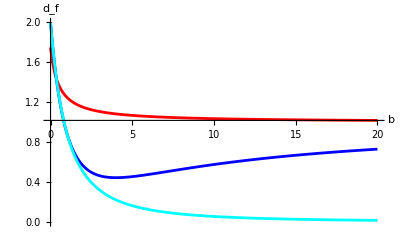

```mathematica
endRange=20;
dfRG2Lwf:=df;

plotSLE=Plot[dfSLE,{b,0,endRange},PlotStyle->Red,PlotRange->All];
plotRG2Lwf=Plot[dfRG2Lwf/.ϵ->2/.a->-2,{b,0,endRange},PlotStyle->Blue,PlotRange->All];
plotRG2L=Plot[dfRG2L/.ϵ->2,{b,0,endRange},PlotStyle->Cyan,PlotRange->All];
Show[{plotSLE,plotRG2Lwf,plotRG2L},PlotRange->{0,2},AxesLabel->{b,Subscript[d, f]}]
```

#### §§ 3d

```mathematica
Limit[dfRG2Lwf,b->∞]
%/.ϵ->1
%/.a->-2
```

1/8 (16-8 ϵ-a ϵ^2)

(8-a)/8

5/4

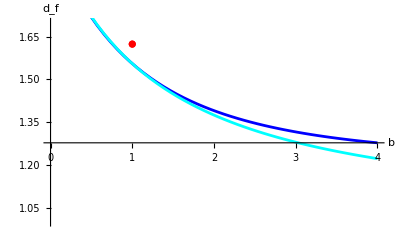

```mathematica
endRange=4;

Plot[dfRG2L/.ϵ->1,{b,0,endRange},PlotStyle->Blue,PlotRange->All];
plotRG2Lwf=Plot[dfRG2Lwf/.ϵ->1/.a->-2,{b,0,endRange},PlotStyle->Blue,PlotRange->All];
plotRG2L=Plot[dfRG2L/.ϵ->1,{b,0,endRange},PlotStyle->Cyan,PlotRange->All];

ListPlot[{{1,1.624}},PlotStyle->Red];

Show[{plotRG2Lwf,plotRG2L,%},PlotRange->{1,1.7},AxesLabel->{b,Subscript[d, f]}]
```

#### Extra data from my simulations

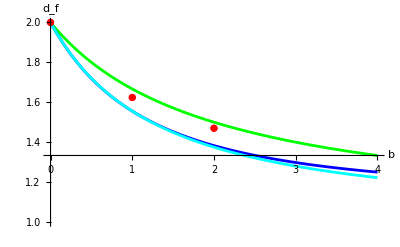

```mathematica
endRange=4;

plotRG1L=Plot[dfRG1L/.ϵ->1,{b,0,endRange},PlotStyle->Green,PlotRange->All];

plotRG2Lwf=Plot[dfRG2Lwf/.ϵ->1/.a->-1,{b,0,endRange},PlotStyle->Blue,PlotRange->All];
plotRG2L=Plot[dfRG2L/.ϵ->1,{b,0,endRange},PlotStyle->Cyan,PlotRange->All];

b0Simulation=ListPlot[{{0,2}},PlotStyle->Red];
b1Simulation=ListPlot[{{1,1.624}},PlotStyle->Red];
b2Simulation=ListPlot[{{2,1.47}},PlotStyle->Red];

Show[{plotRG1L,plotRG2Lwf,plotRG2L,b0Simulation,b1Simulation,b2Simulation},PlotRange->{1,2},AxesLabel->{b,Subscript[d, f]}]
```

### § New (after my simpl)

```mathematica
dfRG1L:=2-b ϵ/(2+b)
dfRG1Lsimp:=2-(b ϵ)/(1+2 b)

dfRG2Lsimp:=Collect[fractalDim,ϵ,FS]

dfRG2Lwf:=dfWF
dfRG2L:=2-b ϵ/(2+b)-b (ϵ/(2+b))^2

(*dfRG2Lsimp:=2-(b ϵ)/(1+2 b)-(b ^2 ϵ^2)/(1+2 b)^2*)(*BAD*)

dfSLE=1+3/(4(2b+1));
```

```mathematica
{dfRG1L,dfRG1Lsimp,dfRG2Lsimp,dfRG2Lwf,dfRG2L,dfRG2Lsimp,dfSLE}/.b->0/.ϵ->2
Limit[{dfRG1L,dfRG1Lsimp,dfRG2Lsimp,dfRG2Lwf,dfRG2L,dfRG2Lsimp,dfSLE},b->∞]/.ϵ->2
```

{2,2,7/4,dfWF,2,7/4,7/4}

{0,1,1,dfWF,0,1,1}

#### §§ 2d

```mathematica
dfRG2Lwf
```

dfWF

Limits

b->∞

```mathematica
Limit[dfRG2Lwf,b->∞]
%/.ϵ->2
%/.a->-2
Limit[dfRG2L,b->∞]
%/.ϵ->2
```

dfWF

dfWF

dfWF

2-ϵ

0

b->0

```mathematica
Limit[dfRG2Lwf,b->0]
%/.ϵ->2
%/.a->-2
Limit[dfRG2L,b->0]
%/.ϵ->2
```

dfWF

dfWF

dfWF

2

2

Plots

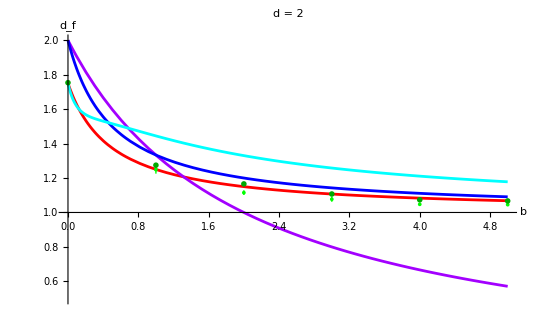

```mathematica
endRange=5;
dfRG2Lwf:=dfWF;


Simulation2d=ListPlot[{{1,1.2490.023},{2,1.1150.013},{3,1.0770.015},{4,1.0470.008},{5,1.0450.006}},PlotStyle->{RGBColor[0, 1, 0],PointSize[0.005]},PlotLegends->Placed[{"Simulation Data (old)"},{Right,Top}]];


Simulation2dGemini=ListPlot[{{0,1.7530.006},{1,1.2750.008},{2,1.16590.0019},{3,1.10730.0024},{4,1.07370.0018},{5,1.06700.0012}(*,{10,1.02510.0012}*)},PlotStyle->{RGBColor[0, 0.66, 0],PointSize[0.1]},PlotMarkers->X,PlotLegends->Placed[{"Simulation Data (Gemini-opt1)"},{Right,Top}]];

plotSLE=Plot[dfSLE,{b,0,endRange},PlotStyle->RGBColor[1, 0, 0],PlotRange->All, PlotLegends->Placed[{Row[{"SLE: ",TraditionalForm[#]}]&@dfSLE},{Right,Top}]];

plotRG1L=Plot[#/.ϵ->2,{b,0,endRange},PlotStyle->RGBColor[0.64, 0, 1],PlotRange->All,PlotLegends->Placed[{Row[{"OLD 1-Loop: ",TraditionalForm[#]}]},{Right,Top}]]&@dfRG1L;

plotRG1Lsimp=Plot[#/.ϵ->2,{b,0,endRange},PlotStyle->RGBColor[0, 0, 1],PlotRange->All,PlotLegends->Placed[{Row[{"NEW 1-Loop: ",TraditionalForm[#]}]},{Right,Top}]]&@dfRG1Lsimp;

plotRG2Lsimp=Plot[#/.ϵ->2,{b,0,endRange},PlotStyle->RGBColor[0, 1, 1],PlotRange->All,PlotLegends->Placed[{Row[{"NEW 2-Loop: ",TraditionalForm[#]}]},{Right,Top}]]&@dfRG2Lsimp;


(*plotRG2Lwf=Plot[dfRG2Lwf/.ϵ->2/.a->+3,{b,0,endRange},PlotStyle->RGBColor[0, 0, 1],PlotRange->All];*)
(*plotRG2L=Plot[dfRG2L/.ϵ->2,{b,0,endRange},PlotStyle->RGBColor[0, 1, 1],PlotRange->All];*)

Show[{plotSLE
,plotRG1L
,plotRG1Lsimp
,plotRG2Lsimp
,Simulation2d
,Simulation2dGemini
(*,plotRG2Lwf
,plotRG2L*)}
,PlotRange->{0.5,2},AxesLabel->{b,Subscript[d, f]},AxesOrigin->{0,1},PlotLabel->Row[{"d = 2"}](*PlotLegends->Placed["AllExpressions", {Right,Top}]*)
]
```

```mathematica
(* The errors are under hestimated *)
```

#### §§ 3d

Limits

b->∞

```mathematica
Limit[dfRG2Lwf,b->∞]
%/.ϵ->1
%/.a->-2

Limit[dfRG2L,b->∞]
%/.ϵ->1
```

dfWF

dfWF

dfWF

2-ϵ

1

b->0

```mathematica
Limit[dfRG2Lwf,b->0]
%/.ϵ->1
%/.a->-2

Limit[dfRG2L,b->0]
%/.ϵ->1
```

dfWF

dfWF

dfWF

2

2

#### Extra data from my simulations

```mathematica
dfRG1Lsimp:=2-(b ϵ)/(1+2 b);
dfSLE=1+3/(4(2b+1));
```

```mathematica
(* It actually seems the corect functional form *)
```

```mathematica
(* I use a big number instead of ∞ as it cannot handle it*)
```

```mathematica
model=2-d b/(a+2b);
nlm=NonlinearModelFit[{{0,2},{1,1.624}(*,{2,1.47}*),{100000,1.5}},{model},{a,d},b]
```

FittedModel[…]

```mathematica
fitFunc=model/.nlm["BestFitParameters"];
```

```mathematica
(* OR *)
```

```mathematica
fitFunc=Fit[{{0,2},{1,1.624}(*,{2,1.47}*),{100000,1.5}},{2,b/(2+b),(b/(2+b))^2},{b}]
```

2.+(0.942013 b^2)/(2+b)^2-(1.442 b)/(2+b)

```mathematica
dfRG1Lsimp
```

2-(b ϵ)/(1+2 b)

```mathematica
Limit[dfRG1Lsimp/.ϵ->1,b->∞]
```

3/2

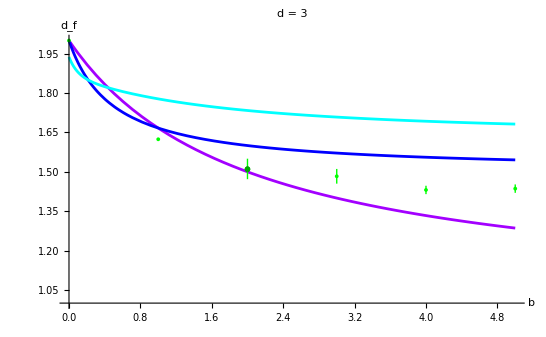

```mathematica
inRange=0;
endRange=5;


Simulation3d=ListPlot[{{0,2},{1,1.624},{2,Around[1.511,0.039]},{3,Around[1.483,0.028]},{4,Around[1.431,0.016]},{5,Around[1.436,0.016]}(*,{10,}*)},PlotStyle->{RGBColor[0, 1, 0],PointSize[0.005]},PlotLegends->Placed[{"Simulation Data (old)"},{Right,Top}]];

Simulation3dGemini=ListPlot[{(*{0,1.7530.006},*){2,Around[1.51,0.01]}(*,{3,1.10730.0024},{4,1.07370.0018},{5,1.06700.0012},{10,1.02510.0012}*)},PlotStyle->{RGBColor[0, 0.66, 0],PointSize[0.1]},PlotMarkers->X,PlotLegends->Placed[{"Simulation Data (Gemini-opt1)"},{Right,Top}]];

plotRG1L=Plot[#/.ϵ->1,{b,inRange,endRange},PlotStyle->RGBColor[0.64, 0, 1],PlotRange->All,PlotLegends->Placed[{Row[{"OLD 1-Loop: ",TraditionalForm[#]}]},{Right,Top}]]&@dfRG1L;

plotRG1Lsimp=Plot[#/.ϵ->1,{b,inRange,endRange},PlotStyle->RGBColor[0, 0, 1],PlotRange->All,PlotLegends->Placed[{Row[{"NEW 1-Loop: ",TraditionalForm[#]}]},{Right,Top}]]&@dfRG1Lsimp;

plotRG2Lsimp=Plot[#/.ϵ->1,{b,0,endRange},PlotStyle->RGBColor[0, 1, 1],PlotRange->All,PlotLegends->Placed[{Row[{"NEW 2-Loop: ",TraditionalForm[#]}]},{Right,Top}]]&@dfRG2Lsimp;

(*plotRG2Lwf=Plot[dfRG2Lwf/.ϵ->1/.a->+3,{b,inRange,endRange},PlotStyle->RGBColor[0, 0, 1],PlotRange->All];
plotRG2L=Plot[dfRG2L/.ϵ->1,{b,inRange,endRange},PlotStyle->RGBColor[0, 1, 1],PlotRange->All];*)


(*fitPlot=Plot[fitFunc,{b,inRange,endRange},PlotStyle->Red,PlotRange->All];*)


Show[{plotRG1L
,plotRG1Lsimp
,plotRG2Lsimp(*,plotRG2Lwf,plotRG2L*)(*,fitPlot*)
,Simulation3d
,Simulation3dGemini
},PlotRange->{1,2},AxesLabel->{b,Subscript[d, f]},AxesOrigin->{0,1},PlotLabel->Row[{"d = 3"}]]
```

```mathematica
fitFunc/.b->3
```

1.46573